# Problem 1 (posted)

```mathematica
If we list all the natural numbers below 10 that are multiples of 3 or 5,we get 3,5,6 and 9. The sum of these multiples is 23.

Find the sum of all the multiples of 3 or 5 below 1000.
```

```mathematica
Timing[
n = 999;  a = 3; b = 5; c =LCM[a, b];
S1 = Sum[ a i, {i, 1, n/a}] ;
S2 = Sum[ b i, {i, 1, n/b}] ;
S3 = Sum[ c i, {i, 1, n/c}] ;  (* undo double counting *)
S = S1 + S2 - S3
]
```

{0.,233168}

# Problem 3 (posted)

```mathematica
argest prime factor
Problem 3
The prime factors of 13195 are 5,7,13 and 29.

What is the largest prime factor of the number 600851475143?
```

```mathematica
FactorInteger[600851475143][[-1]][[1]]
```

6857

# Prob 4

```mathematica
PalinQ[M_] :=Module[ {   j, result =True},
{digits, numDigits} =RealDigits[M];
For[j=1, j<(numDigits+1)/2, ++j, 
If[ digits[[j]] ≠ digits[[-j]], result = False; Break[];];
];
result];

MAX = 0;
For[ N1=999, N1 > 100, N1--,{
(* Print[N1]; *)
For[N2 = 999, N2 >= N1, N2--,
{
N1N2 = N1*N2;
If[  PalinQ[N1N2] , Break[]]; 
}
];
If[ N1N2 > MAX && PalinQ[N1N2], {MAX = N1N2, Print[N1, " ", N2, " ", MAX ] } ];
If[ N1 < MAX/999, Break[]];
}
];
```

924 962 888888

913 993 906609

# Problem 5 (posted)

```mathematica
2520 is the smallest number that can be divided by each of the numbers from 1 to 10 without any remainder.What is the smallest positive number that is evenly divisible by all of the numbers from 1 to 20?
```

```mathematica
2^4  3^2  5 7 11 13 17 19
```

232792560

# Problem 6 (posted)

```mathematica
The sum of the squares of the first ten natural numbers is,12+22+...+102=385
The square of the sum of the first ten natural numbers is,(1+2+...+10)2=552=3025
Hence the difference between the sum of the squares of the first ten natural numbers and the square of the sum is 3025−385=2640.

Find the difference between the sum of the squares of the first one hundred natural numbers and the square of the sum.
```

```mathematica
F[n_] :=  (Sum[ i, {i, 1, n}])^2  - Sum[ i^2, {i, 1, n}]  //Simplify
F[100]
```

25164150

# Prob 7 (posted)

```mathematica
Prime[10001]
```

104743

# Prob 8

```mathematica
9 9 8 7 9
```

40824

# Prob 9

```mathematica
Solve[ c/√2 - (1000.- c)/2  ==0, c]
```

{{c→414.214}}

```mathematica
Solve[ 1. + (999-c)^2 == c^2, c]
```

{{c→499.501}}

```mathematica
n = 20;
m = 5;
a = (n^2- m^2)
b = 2 n m
c = (n^2+ m^2)
a^2+ b^2- c^2
a b c
```

375

200

425

0

31875000

# Prob 10

```mathematica
Prime[148933]
Prime[148934]
Sum[ Prime[i], {i, 1, 148933}]
```

1999993

2000003

142913828922

# problem 11

```mathematica
SetDirectory["C:/Minqiang/ProjectEuler"];
data = Import["problem11.txt", "Table"];
prod1[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[i-3<1, 0, Product[mat[[i-k,j]] , {k, 0, 3}]];
{result, 1}]
prod2[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[i-3<1 || j+3 > L , 0, Product[mat[[i-k,j+k]] , {k, 0, 3}]];
{result,2}]
prod3[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[j+3>L, 0, Product[mat[[i,j+k]] , {k, 0, 3}]];
{result,3}]
prod4[mat_, i_, j_] := Module[ {L= Length[mat], result},
result = If[i+3>L || j+3 >L, 0, Product[mat[[i+k,j+k]] , {k, 0, 3}]];
{result,4}]
prod5[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[i+3>L, 0, Product[mat[[i+k,j]] , {k, 0, 3}]];
{result,5}]
prod6[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[i+3>L || j-3<1, 0, Product[mat[[i+k,j-k]] , {k, 0, 3}]];
{result,6}]
prod7[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[j-3<1, 0, Product[mat[[i,j-k]] , {k, 0, 3}]];
{result,7}]
prod8[mat_, i_, j_] := Module[ {L = Length[mat], result},
result = If[i-3<1 || j-3< 1, 0, Product[mat[[i-k, j-k]] , {k,0, 3}]];
{result,8}]

max = 0;
direction = 0;

For[i=1, i<Length[data], ++i,
For[j=1,j<Length[data], ++j,
p1 = prod1[data, i, j];
p2 = prod2[data, i, j];
p3 = prod3[data, i, j];
p4 = prod4[data, i, j];
p5 = prod5[data, i, j];
p6 = prod6[data, i, j];
p7 = prod7[data, i, j];
p8 = prod8[data, i, j];
{thismax, thisdirection} = Last[Sort[{p1, p2, p3, p4, p5, p6, p7, p8}]];
If[ thismax > max, max = thismax; direction = thisdirection;
Print[i, ", ", j,", ", thismax,", ", thisdirection];
];
]
]
```

1, 1, 1651104, 5

1, 3, 6414210, 5

1, 4, 24468444, 6

1, 14, 34826064, 6

2, 13, 41076896, 6

7, 16, 51267216, 5

13, 7, 70600674, 6

{1651104,5}

# Problem 12

```mathematica
For[n=1,True,++n,num=n (n+1)/2;
If[Length[Divisors[num]]>500,Print[num];Break[]];];
```

# Prob 13

```mathematica
Total[ {37107287533902102798797998220837590246510135740250,
46376937677490009712648124896970078050417018260538,
74324986199524741059474233309513058123726617309629,
91942213363574161572522430563301811072406154908250,
23067588207539346171171980310421047513778063246676,
89261670696623633820136378418383684178734361726757,
28112879812849979408065481931592621691275889832738,
44274228917432520321923589422876796487670272189318,
47451445736001306439091167216856844588711603153276,
70386486105843025439939619828917593665686757934951,
62176457141856560629502157223196586755079324193331,
64906352462741904929101432445813822663347944758178,
92575867718337217661963751590579239728245598838407,
58203565325359399008402633568948830189458628227828,
80181199384826282014278194139940567587151170094390,
35398664372827112653829987240784473053190104293586,
86515506006295864861532075273371959191420517255829,
71693888707715466499115593487603532921714970056938,
54370070576826684624621495650076471787294438377604,
53282654108756828443191190634694037855217779295145,
36123272525000296071075082563815656710885258350721,
45876576172410976447339110607218265236877223636045,
17423706905851860660448207621209813287860733969412,
81142660418086830619328460811191061556940512689692,
51934325451728388641918047049293215058642563049483,
62467221648435076201727918039944693004732956340691,
15732444386908125794514089057706229429197107928209,
55037687525678773091862540744969844508330393682126,
18336384825330154686196124348767681297534375946515,
80386287592878490201521685554828717201219257766954,
78182833757993103614740356856449095527097864797581,
16726320100436897842553539920931837441497806860984,
48403098129077791799088218795327364475675590848030,
87086987551392711854517078544161852424320693150332,
59959406895756536782107074926966537676326235447210,
69793950679652694742597709739166693763042633987085,
41052684708299085211399427365734116182760315001271,
65378607361501080857009149939512557028198746004375,
35829035317434717326932123578154982629742552737307,
94953759765105305946966067683156574377167401875275,
88902802571733229619176668713819931811048770190271,
25267680276078003013678680992525463401061632866526,
36270218540497705585629946580636237993140746255962,
24074486908231174977792365466257246923322810917141,
91430288197103288597806669760892938638285025333403,
34413065578016127815921815005561868836468420090470,
23053081172816430487623791969842487255036638784583,
11487696932154902810424020138335124462181441773470,
63783299490636259666498587618221225225512486764533,
67720186971698544312419572409913959008952310058822,
95548255300263520781532296796249481641953868218774,
76085327132285723110424803456124867697064507995236,
37774242535411291684276865538926205024910326572967,
23701913275725675285653248258265463092207058596522,
29798860272258331913126375147341994889534765745501,
18495701454879288984856827726077713721403798879715,
38298203783031473527721580348144513491373226651381,
34829543829199918180278916522431027392251122869539,
40957953066405232632538044100059654939159879593635,
29746152185502371307642255121183693803580388584903,
41698116222072977186158236678424689157993532961922,
62467957194401269043877107275048102390895523597457,
23189706772547915061505504953922979530901129967519,
86188088225875314529584099251203829009407770775672,
11306739708304724483816533873502340845647058077308,
82959174767140363198008187129011875491310547126581,
97623331044818386269515456334926366572897563400500,
42846280183517070527831839425882145521227251250327,
55121603546981200581762165212827652751691296897789,
32238195734329339946437501907836945765883352399886,
75506164965184775180738168837861091527357929701337,
62177842752192623401942399639168044983993173312731,
32924185707147349566916674687634660915035914677504,
99518671430235219628894890102423325116913619626622,
73267460800591547471830798392868535206946944540724,
76841822524674417161514036427982273348055556214818,
97142617910342598647204516893989422179826088076852,
87783646182799346313767754307809363333018982642090,
10848802521674670883215120185883543223812876952786,
71329612474782464538636993009049310363619763878039,
62184073572399794223406235393808339651327408011116,
66627891981488087797941876876144230030984490851411,
60661826293682836764744779239180335110989069790714,
85786944089552990653640447425576083659976645795096,
66024396409905389607120198219976047599490197230297,
64913982680032973156037120041377903785566085089252,
16730939319872750275468906903707539413042652315011,
94809377245048795150954100921645863754710598436791,
78639167021187492431995700641917969777599028300699,
15368713711936614952811305876380278410754449733078,
40789923115535562561142322423255033685442488917353,
44889911501440648020369068063960672322193204149535,
41503128880339536053299340368006977710650566631954,
81234880673210146739058568557934581403627822703280,
82616570773948327592232845941706525094512325230608,
22918802058777319719839450180888072429661980811197,
77158542502016545090413245809786882778948721859617,
72107838435069186155435662884062257473692284509516,
20849603980134001723930671666823555245252804609722,
53503534226472524250874054075591789781264330331690}]
```

5537376230390876637302048746832985971773659831892672

# Problem 14 (posted)

```mathematica
The following iterative sequence is defined for the set of positive integers:n->n/2 (n is even)
n->3n+1 (n is odd)

Using the rule above and starting with 13,we generate the following sequence:13->40->20->10->5->16->8->4->2->1
It can be seen that this sequence (starting at 13 and finishing at 1) contains 10 terms.Although it has not been proved yet (Collatz Problem),it is thought that all starting numbers finish at 1.

Which starting number,under one million,produces the longest chain?NOTE:Once the chain starts the terms are allowed to go above one million.
```

```mathematica
AbsoluteTiming[ClearAll["Global`*"];
maxlen=0;
maxn=0;
$RecursionLimit=1000000;

collatz[1]=1;
collatz[2]=2;
(*If n is odd,speed up a little bit by doing 2 steps same time*)collatz[n_Integer]:=collatz[n]=If[OddQ[n],collatz[(3 n+1)/2]+2,collatz[n/2]+1];

For[n=1,n<1000000,++n,len=collatz[n];
If[len>maxlen,maxlen=len;maxn=n];];
maxn]
```

{12.949741,837799}

# Problem 16 (posted)

```mathematica
215=32768 and the sum of its digits is 3+2+7+6+8=26.

What is the sum of the digits of the number 21000?
```

```mathematica
Total[IntegerDigits[2^1000]]
```

1366

# Prob 17 (posted)

```mathematica
If the numbers 1 to 5 are written out in words:one,two,three,four,five,then there are 3+3+5+4+4=19 letters used in total.If all the numbers from 1 to 1000 (one thousand) inclusive were written out in words,how many letters would be used?NOTE:Do not count spaces or hyphens.For example,342 (three hundred and forty-two) contains 23 letters and 115 (one hundred and fifteen) contains 20 letters.The use of "and" when writing out numbers is in compliance with British usage.
```

```mathematica
AbsoluteTiming[
L[0]=0;
L[1]=3; (* one *)
L[2]=3; (* two *)
L[3]=5;(* three *)
L[4]=4; (* four *)
L[5]=4; (* five *)
L[6]=3;(* six *)
L[7]=5; (* seven *)
L[8]=5; (* eight *)
L[9]=4; (* nine *)
L[10] = 3; (* ten *)
L[11] = 6; (* eleven *)
L[12] = 6; (* twelve *)
L[13] = 8; (* thirteen *)
L[14] = 8; (* fourteen *)
L[15] = 7; (* fifteen *)
L[16] = 7; (* sixteen *)
L[17] = 9; (* seventeen *)
L[18] = 8; (* eighteen *)
L[19] = 8; (* nineteen *)
L[20] = 6; (* twenty *)
L[30] = 6;(* thirty *)
L[40] = 5; (* forty *)
L[50] = 5; (* fifty *)
L[60] = 5; (* sixty *)
L[70] = 7;(* seventy *)
L[80] = 6; (* eighty *)
L[90] = 6; (* ninety *)
L[1000] = 3+8;
L[n_] /; n<=99 = L[ Mod[n, 10] ] + L[  n- Mod[n,10]];
L[n_] /; n>99:= L[ Floor[n/100]]+7+3 If[Mod[n,100]>0, 1, 0]+ L[ Mod[n, 100]] ;
Sum[ L[n], {n, 1, 1000}]
]
```

{0.015,21124}

# Problem 18

{{75},{95,64},{17,47,82},{18,35,87,10},{20,4,82,47,65},{19,1,23,75,3,34},{88,2,77,73,7,63,67},{99,65,4,28,6,16,70,92},{41,41,26,56,83,40,80,70,33},{41,48,72,33,47,32,37,16,94,29},{53,71,44,65,25,43,91,52,97,51,14},{70,11,33,28,77,73,17,78,39,68,17,57},{91,71,52,38,17,14,91,43,58,50,27,29,48},{63,66,4,68,89,53,67,30,73,16,69,87,40,31},{4,62,98,27,23,9,70,98,73,93,38,53,60,4,23}}

```mathematica
data[[2,1]]
```

95

```mathematica
Length[data]
```

15

```mathematica
ClearAll["Global`*"];
SetDirectory["C:/Minqiang/ProjectEuler"];
data = Import["problem18.txt", "Table"];
maxsum[Length[data],j_] := maxsum[Length[data],j] = data[ [Length[data],j]];
maxsum[i_,j_] := maxsum[i,j] =data[[i,j]]+ Max[maxsum[i+1,j] , maxsum[i+1,j+1] ];
maxsum[1,1]
```

1074

# Problem 19

```mathematica
days = DayRange[{1901,1,1},{2000,12,31}];
Length[Select[days, (#[[3]]==1&& DayName[#]==Sunday)&]]
```

171

# Prob 21

Let d(n) be defined as the sum of proper divisors of n (numbers less than n which divide evenly into n).If d(a)=b and d(b)=a,where a!=b,then a and b are an amicable pair and each of a and b are called amicable numbers.For example,the proper divisors of 220 are 1,2,4,5,10,11,20,22,44,55 and 110;therefore d(220)=284. The proper divisors of 284 are 1,2,4,71 and 142;so d(284)=220.

Evaluate the sum of all the amicable numbers under 10000.

```mathematica
Upper = 10000;
dfun[M_] := Total[Divisors[M]] - M;
Amicable[M_] := (dfun[dfun[M]] == M && dfun[M] ≠ M);
For[
i=2;SUM =0,
i<10000,
i++,
{
If[Amicable[i], SUM = SUM+i];
}
];
SUM
```

31626

# Problem 22

```mathematica
SetDirectory["C:/Minqiang/ProjectEuler"];
data=Sort[Flatten[Import["problem22.txt","Table"]]];
v["A"]=1;
v["B"]=2;
v["C"]=3;
v["D"]=4;
v["E"]=5;
v["F"]=6;
v["G"]=7;
v["H"]=8;
v["I"]=9;
v["J"]=10;
v["K"]=11;
v["L"]=12;
v["M"]=13;
v["N"]=14;
v["O"]=15;
v["P"]=16;
v["Q"]=17;
v["R"]=18;
v["S"]=19;
v["T"]=20;
v["U"]=21;
v["V"]=22;
v["W"]=23;
v["X"]=24;
v["Y"]=25;
v["Z"]=26;
f[s_]:=Sum[v[StringTake[s,{n}]],{n,1,StringLength[s]}];
Sum[f[data[[i]]]*i,{i,1,Length[data]}]
```

871198282

# problem 23 (posted)

```mathematica
A perfect number is a number for which the sum of its proper divisors is exactly equal to the number.For example,the sum of the proper divisors of 28 would be 1+2+4+7+14=28,which means that 28 is a perfect number.A number n is called deficient if the sum of its proper divisors is less than n and it is called abundant if this sum exceeds n.As 12 is the smallest abundant number,1+2+3+4+6=16,the smallest number that can be written as the sum of two abundant numbers is 24. By mathematical analysis,it can be shown that all integers greater than 28123 can be written as the sum of two abundant numbers.However,this upper limit cannot be reduced any further by analysis even though it is known that the greatest number that cannot be expressed as the sum of two abundant numbers is less than this limit.Find the sum of all the positive integers which cannot be written as the sum of two abundant numbers.
```

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];
max = 28123.;
AbundantQ[1] = False; 
AbundantQ[n_]:= AbundantQ[n] =  If[ Total[Divisors[n]]> 2 n,
 True, False];
list = Select[ Range[max/2.], AbundantQ];
notsumAbundantQ[n_] := Module[ {i,result=True}, 
halfn = n/2;
For[i=1, list[[i]]≤ halfn, ++i,
If[   AbundantQ[n-list[[i]]], result = False; Break[] ];
];
result];
Total[Select[ Range[max], notsumAbundantQ ]]
]
```

{18.93308,4179871}

# Prob 24

A permutation is an ordered arrangement of objects. For example, 3124 is one possible permutation of the digits 1, 2, 3 and 4. If all of the permutations are listed numerically or alphabetically, we call it lexicographic order. The lexicographic permutations of 0, 1 and 2 are:

012   021   102   120   201   210

What is the millionth lexicographic permutation of the digits 0, 1, 2, 3, 4, 5, 6, 7, 8 and 9?

```mathematica
IsPermutation[i_] := (Sort[IntegerDigits[i] ]== {0, 1, 2, 3, 4,5,6,7,8,9});
order = 999983;
For[
i=2783906541,
i<9876543210,
i=i+9,
{
If[IsPermutation[i], order++];
If[Mod[Order, 10000]==0, Print[i] ];
If[order == 1000000,  Print[i]; Break[] ];
}

];
```

2783915460

# Problem 25 (posted)

The Fibonacci sequence is defined by the recurrence relation:

Fn = Fn−1 + Fn−2, where F1 = 1 and F2 = 1.
Hence the first 12 terms will be:

F1 = 1
F2 = 1
F3 = 2
F4 = 3
F5 = 5
F6 = 8
F7 = 13
F8 = 21
F9 = 34
F10 = 55
F11 = 89
F12 = 144
The 12th term, F12, is the first term to contain three digits.

What is the first term in the Fibonacci sequence to contain 1000 digits?

```mathematica
AbsoluteTiming[
For[i=1,True,i++,
If[ Ceiling[Log[10., Fibonacci[i]]] == 1000, Break[];  ];
];
i]
```

{0.11201,4782}

# Problem 26 (posted)

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];
maxlen = 0;
maxn = 0;
For[n = 1, n<1000,++n,
len = Length[RealDigits[1/n][[1,-1]]];
If[ len > maxlen, maxlen = len; maxn = n];
];
maxn
]
```

{0.04,983}

# problem 27

```mathematica
Euler discovered the remarkable quadratic formula:n.b2+n+41

It turns out that the formula will produce 40 primes for the consecutive values n=0 to 39. However,when n=40,402+40+41=40(40+1)+41 is divisible by 41,and certainly when n=41,41.b2+41+41 is clearly divisible by 41.

The incredible formula n.b2−79n+1601 was discovered,which produces 80 primes for the consecutive values n=0 to 79. The product of the coefficients,−79 and 1601,is−126479.

Considering quadratics of the form:n.b2+an+b,where|a| <1000 and|b| <1000

where|n|is the modulus/absolute value of n
e.g. |11| =11 and|−4| =4
Find the product of the coefficients,a and b,for the quadratic expression that produces the maximum number of primes for consecutive values of n,starting with n=0.
```

```mathematica
NumPrimes[a_,b_]:=Module[{n},For[n=0,n<1000,n++,If[!PrimeQ[n^2+a n+b],Break[]];];
n];
MaxNum=0;
limit=999;
For[a=-limit,a≤limit,a++,For[b=-limit,b≤limit,b++,{num=NumPrimes[a,b];
If[num>MaxNum,Print[a,", ",b," ,",num];MaxNum=num];}]]
```

-999, -997 ,1

-999, -953 ,2

-999, -863 ,4

-999, -383 ,5

-999, -23 ,10

-999, 61 ,11

-991, 677 ,18

-897, 409 ,20

-539, 641 ,21

-61, 971 ,71

# Problem 28 (posted)

```mathematica
Starting with the number 1 and moving to the right in a clockwise direction a 5 by 5 spiral is formed as follows:21 22 23 24 25
20 7 8 9 10
19 6 1 2 11
18 5 4 3 12
17 16 15 14 13

It can be verified that the sum of the numbers on the diagonals is 101.

What is the sum of the numbers on the diagonals in a 1001 by 1001 spiral formed in the same way?
```

```mathematica
Timing[
len = 1001;
max = (len-1)/2;
T1 = Sum[ (2n+1)^2, {n , 1, max}];
T2 = Sum[ (2n)^2 + 1, {n , 1, max}];
T3 = Sum[ (2n)^2 + 2n + 1, {n , 1, max}];
T4 = Sum[ (2n)^2 - 2n +1, {n, 1, max}];
1+ Total[{ T1, T2, T3, T4}]
]
```

{0.,669171001}

# Problem 29 (posted)

```mathematica
Consider all integer combinations of ab for 2≤a≤5 and 2≤b≤5:22=4,23=8,24=16,25=32
32=9,33=27,34=81,35=243
42=16,43=64,44=256,45=1024
52=25,53=125,54=625,55=3125
If they are then placed in numerical order,with any repeats removed,we get the following sequence of 15 distinct terms:4,8,9,16,25,27,32,64,81,125,243,256,625,1024,3125

How many distinct terms are in the sequence generated by ab for 2≤a≤100 and 2≤b≤100?
```

```mathematica
I use DeleteDuplicates instead of Union.I found DeleteDuplicates to be faster than Union for large lists (for example,if 100 is changed to 1000).
```

```mathematica
Timing[Length[DeleteDuplicates[Flatten[Table[a^b, {a, 2, 100}, {b, 2, 100}]]]]]
```

{0.031,9183}

# Problem 30 (posted)

Surprisingly there are only three numbers that can be written as the sum of fourth powers of their digits:

1634 = 14 + 64 + 34 + 44
8208 = 84 + 24 + 04 + 84
9474 = 94 + 44 + 74 + 44
As 1 = 14 is not a sum it is not included.

The sum of these numbers is 1634 + 8208 + 9474 = 19316.

Find the sum of all the numbers that can be written as the sum of fifth powers of their digits.

```mathematica
Reduce[ 10^n < n 9^5., n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0000169357<n<5.51257

```mathematica
So the number at most is a 6-digit number
cannot be 2-digit number by analyzing last digit
3-digit?: since i^5 and i have same digits, the first two digits must be j and 10-j (j not 0).
```

```mathematica
No solution. So must be 4 digit number or 5-digit number.
```

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];
SUM=0;
(* It can be rigorously shown that the number cannot have fewer than 3 digits by analyzing the last digits, and cannot be larger than 6*9^5.
A useful observation is that for any number, the last digit of its fifth power is the same as its own last digit.
*)
For[n=1000,n<=6 9^5,++n,
If[  Total[  IntegerDigits[n]^5 ]== n, SUM = SUM+n;];
];
SUM]
```

{2.24413,443839}

# Problem 31 (posted)

```mathematica
In England the currency is made up of pound,£,and pence,p,and there are eight coins in general circulation:1p,2p,5p,10p,20p,50p,£1 (100p) and £2 (200p).It is possible to make £2 in the following way:1×£1+1×50p+2×20p+1×5p+1×2p+3×1p
How many different ways can £2 be made using any number of coins?
```

```mathematica
ClearAll["Global`*"]


list  = {1, 2, 5, 10, 20, 50, 100, 200};
(*n is the amount of money we want to break.i is the number of coins we can use*)
numways[n_, 1]=1;
numways[n_, i_] :=numways[n,i-1]/; n<i 
numways[n_, i_] :=  numways[n, i] = Module[ {k, kmax},
kmax = Floor[n/list[[i]]];
Sum[ numways[n- k *list[[i]], i-1 ] , {k, 1, kmax}] + numways[n, i-1]
];

Timing[numways[200, 8]]
```

{0.,73682}

# Problem 32 (posted)

```mathematica
We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once;for example,the 5-digit number,15234,is 1 through 5 pandigital.The product 7254 is unusual,as the identity,39×186=7254,containing multiplicand,multiplier,and product is 1 through 9 pandigital.Find the sum of all products whose multiplicand/multiplier/product identity can be written as a 1 through 9 pandigital.HINT:Some products can be obtained in more than one way so be sure to only include it once in your sum.
```

```mathematica
Timing[
imax =  Floor[Sqrt[100000]]; (* If i > imax, then j has at least 3 digits, and product p has at least 6 digits, with total exceeding 9 *)

jmax = 8976; (* j cannot have 5 digits, and j has to be smaller than p, so first digit of j cannot be 9 *)

list = Range[9];
prodset= {};

For[i= 1, i<imax, ++i,
{digitsi, numdigitsi }= RealDigits[i];
For[j=Max[i+1, imax], j<= jmax, ++j,
{digitsj, numdigitsj }= RealDigits[j];
p = i*j;
{digitsp, numdigitsp }= RealDigits[p];
If[ numdigitsp + numdigitsi + numdigitsj > 9, Break[]]; If[ Sort[ Join[digitsi, digitsj, digitsp] ] == list, AppendTo[prodset, p]; ];
];
];

Total[Union[prodset]]
]
```

{0.312,20600}

# Problem 33 (posted)

```mathematica
The fraction 49/98 is a curious fraction,as an inexperienced mathematician in attempting to simplify it may incorrectly believe that 49/98=4/8,which is correct,is obtained by cancelling the 9s.We shall consider fractions like,30/50=3/5,to be trivial examples.There are exactly four non-trivial examples of this type of fraction,less than one in value,and containing two digits in the numerator and denominator.If the product of these four fractions is given in its lowest common terms,find the value of the denominator.
```

```mathematica
prod =1;
For[n=11,n≤98,++n,
If[Mod[n, 10] ==0, Continue[]];
ndigits = IntegerDigits[n];
n1 = ndigits[[1]];
n2 = ndigits[[2]];
For[d=n+1, d≤99, ++d,
If[Mod[d,10]==0, Continue[]];
ddigits = IntegerDigits[d];
d1 = ddigits[[1]];
d2 = ddigits[[2]];
If[n/d == n1/d2 && n2 == d1 , prod=prod*n/d];
];
]
prod//Simplify
```

1/100

# Problem 34

```mathematica
145 is a curious number,as 1!+4!+5!=1+24+120=145.

Find the sum of all numbers which are equal to the sum of the factorial of their digits.Note:as 1!=1 and 2!=2 are not sums they are not included.
```

```mathematica
9!
```

362880

```mathematica
Reduce[  10^n ≤ n 9! 1., n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2.75575×10^-6≤n≤6.36346

```mathematica
Timing[
sum =0;
list = Table[i!, {i, 0, 9}];
For[n=11, n<10^6, ++n,
{digits, numdigits} = RealDigits[n];
If[ Total[list[[digits+1]]] == n, sum = sum + n; ]
];
sum
]
```

{11.7,40730}

# Prob 35

```mathematica
The number,197,is called a circular prime because all rotations of the digits:197,971,and 719,are themselves prime.There are thirteen such primes below 100:2,3,5,7,11,13,17,31,37,71,73,79,and 97.

How many circular primes are there below one million?
```

```mathematica
Solution: The digits must be 1,3,7,9
```

```mathematica
Prime[78500]
```

1000033

```mathematica
perm[list_] :=Append[ Drop[list, 1], list[[1]]]
num = 0;
For[j=1, j<78500, ++j,
p=Prime[j];
result = True;
list = RealDigits[p][[1]];
For[i=1, i< Length[list], ++i,
list = perm[list];
If[!PrimeQ[FromDigits[list]],result=False;Break[]];
];
If[result == True, num++;];
]
num
```

55

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended.

# Problem 37 (program not optimized, should save intermediate results)

```mathematica
The number 3797 has an interesting property.Being prime itself,it is possible to continuously remove digits from left to right,and remain prime at each stage:3797,797,97,and 7. Similarly we can work from right to left:3797,379,37,and 3.

Find the sum of the only eleven primes that are both truncatable from left to right and right to left.NOTE:2,3,5,and 7 are not considered to be truncatable primes.
```

```mathematica
num  = 0;
sum = 0;
For[n = 11, n <= 1000000, n = n+2,
list = RealDigits[n][[1]];
listleftintegers = Drop[Map[FromDigits, FoldList[ Drop[#,-1] &, list, list] ], -1];
listrightintegers = Drop[Map[FromDigits, FoldList[ Drop[#,1] &, list, list] ], -1];
listQ = Fold[And, True, Map[PrimeQ, listleftintegers]] &&  Fold[And, True, Map[PrimeQ, listrightintegers]];
If[ listQ, Print[n];num++; sum=sum+n];
If[num == 11, Break[]];
]
sum
```

23

37

53

73

313

317

373

797

3137

3797

739397

748317

# Problem 38 (posted)

```mathematica
Take the number 192 and multiply it by each of 1,2,and 3:192×1=192
192×2=384
192×3=576
By concatenating each product we get the 1 to 9 pandigital,192384576. We will call 192384576 the concatenated product of 192 and (1,2,3)

The same can be achieved by starting with 9 and multiplying by 1,2,3,4,and 5,giving the pandigital,918273645,which is the concatenated product of 9 and (1,2,3,4,5).What is the largest 1 to 9 pandigital 9-digit number that can be formed as the concatenated product of an integer with (1,2,...,n) where n>1?
```

```mathematica
AbsoluteTiming[
max = 0;
For[n=2, n<9, ++n,
list = Range[n];
For[i=1, i< 10^Ceiling[9/n], ++i,
digits = Flatten[IntegerDigits[list*i]];
If[Length[digits]>9, Break[];];
If[Length[digits]<9, Continue[];];
If[ Sort[digits] == Range[9], number = FromDigits[digits];
If[ number > max, max = number; ];
];
];
];
max
]
```

{0.20501,932718654}

# Problem 39 (posted)

```mathematica
Problem 39
If p is the perimeter of a right angle triangle with integral length sides,{a,b,c},there are exactly three solutions for p=120.

{20,48,52},{24,45,51},{30,40,50}

For which value of p≤1000,is the number of solutions maximised?
```

```mathematica
Timing[
ClearAll["Global`*"];

limit = 1000;
numsols=Table[0,{i,limit}];(* record number of solutions for each p *)

(* the shortest side cannot be longer than this *)amax=x/.Solve[2 x+Sqrt[2] x==limit,x][[1]];

For[a=1,a≤amax,++a,
bmax=x/.Solve[a+x+Sqrt[a^2+x^2]==limit,x][[1]];
For[b=a,b≤bmax,++b,
c=Sqrt[a^2+b^2];
If[IntegerQ[c],numsols[[a+b+c]]++];
];
];

Position[numsols,Max[numsols]]
]
```

{1.388,{{840}}}

# Problem 40 (posted)

```mathematica
An irrational decimal fraction is created by concatenating the positive integers:0.123456789101112131415161718192021...

It can be seen that the 12th digit of the fractional part is 1.

If dn represents the nth digit of the fractional part,find the value of the following expression.d1×d10×d100×d1000×d10000×d100000×d1000000
```

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];Needs["Combinatorica`"];
TotalDigits[1] =9;TotalDigits[n_] := TotalDigits[n] = n*9*10^(n-1) + TotalDigits[n-1];
list = Table[ TotalDigits[i],{i,1,6}];

prod = 1;
For[j=1, j≤6, ++j,
n = 10^j;
k = Floor[ BinarySearch[list, n] ];
ExtraDigits = n - list[[k]];
{AdditionalNumbers,Extra}  = QuotientRemainder[ExtraDigits,k+1];
LastInteger = 10^k + AdditionalNumbers;
If[ Extra == 0,Result =IntegerDigits[LastInteger][[-1]],
Result = IntegerDigits[LastInteger+1] [[Extra]] ;
];
prod = prod * Result;
];
prod
]
```

{0.008,210}

# Problem 41 (posted)

```mathematica
We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once.For example,2143 is a 4-digit pandigital and is also prime.What is the largest n-digit pandigital prime that exists?
```

```mathematica
Timing[
(* the number of digits for the prime can only be 1, 4, or 7 since otherwise the number is divisible by 3 *)
list = Table[ Sum[i, {i, 1, n}], {n, 1, 9}];
validnumdigits = Select[Range[9], Mod[list[[#]], 3] != 0& ] ;

For[ i=Length[validnumdigits], i≥1, --i,
digitlist = Transpose[Permutations[ Range[ validnumdigits[[i]] ]]];
primelist= Select[ FromDigits[digitlist], PrimeQ];
If[Length[primelist]>0, primesought = Last[primelist]; Break[]];
];

primesought
]
```

{0.,7652413}

# Problem 42

```mathematica
ClearAll["Global`*"];
SetDirectory["C:/Minqiang/ProjectEuler"];
data=Sort[Flatten[Import["problem42.txt","Table"]]];
v["A"]=1;
v["B"]=2;
v["C"]=3;
v["D"]=4;
v["E"]=5;
v["F"]=6;
v["G"]=7;
v["H"]=8;
v["I"]=9;
v["J"]=10;
v["K"]=11;
v["L"]=12;
v["M"]=13;
v["N"]=14;
v["O"]=15;
v["P"]=16;
v["Q"]=17;
v["R"]=18;
v["S"]=19;
v["T"]=20;
v["U"]=21;
v["V"]=22;
v["W"]=23;
v["X"]=24;
v["Y"]=25;
v["Z"]=26;
f[s_]:=Sum[v[StringTake[s,{n}]],{n,1,StringLength[s]}];
TNQ[n_]:=TNQ[n]=If[IntegerQ[1/2 (-1+Sqrt[1+8 n])],True,False];Count[TNQ/@(f/@data),True]
```

162

# Problem 43

```mathematica
The number,1406357289,is a 0 to 9 pandigital number because it is made up of each of the digits 0 to 9 in some order,but it also has a rather interesting sub-string divisibility property.Let d1 be the 1st digit,d2 be the 2nd digit,and so on.In this way,we note the following:d2d3d4=406 is divisible by 2
d3d4d5=063 is divisible by 3
d4d5d6=635 is divisible by 5
d5d6d7=357 is divisible by 7
d6d7d8=572 is divisible by 11
d7d8d9=728 is divisible by 13
d8d9d10=289 is divisible by 17
Find the sum of all 0 to 9 pandigital numbers with this property.
```

```mathematica
17*58
```

986

```mathematica
FactorInteger[986]
```

{{2,1},{17,1},{29,1}}

# Problem 45 (posted)

```mathematica
Triangle,pentagonal,and hexagonal numbers are generated by the following formulae:Triangle Tn=n(n+1)/2 1,3,6,10,15,...
Pentagonal Pn=n(3n−1)/2 1,5,12,22,35,...
Hexagonal Hn=n(2n−1) 1,6,15,28,45,...
It can be verified that T285=P165=H143=40755.

Find the next triangle number that is also pentagonal and hexagonal.
```

```mathematica
ClearAll["Global`*"];
Timing[
For[n=144, True, ++n,
If[ IntegerQ[ 1/6 (1+√(1-24 n + 48n^2))], result = n; Break[];]
];
result * (2 result -1)
]
```

{0.967206,1533776805}

# problem 46 (posted)

```mathematica
Problem 46
It was proposed by Christian Goldbach that every odd composite number can be written as the sum of a prime and twice a square.9=7+2×12
15=7+2×22
21=3+2×32
25=7+2×32
27=19+2×22
33=31+2×12

It turns out that the conjecture was false.What is the smallest odd composite that cannot be written as the sum of a prime and twice a square?
```

```mathematica
Timing[
(* GoldBachQ is the test function to see if a nonprime is good *)GoldBachQimpl[n_]:=Module[{z=Floor[Sqrt[n/2]],i,result=False},For[i=1,i≤z,++i,If[PrimeQ[n-2*i^2],result=True;Break[]];];
result];
GoldBachQ[n_]:=If[PrimeQ[n],True,GoldBachQimpl[n]];

For[n=3,True,n=n+2,
If[!GoldBachQ[n],offendingnum=n;Break[]];
];

offendingnum
]
```

{0.14,5777}

```mathematica
Other people's solution, slow!!
```

```mathematica
Timing[
n=10^5;
a=Range[3,n,2];
q=IntegerPart[Sqrt[n/2]];
p=PrimePi[n];
Do[a=Complement[a,Table[Prime[k]+2*j^2,{k,p}]],{j,0,q}];
a
]
```

{2.964,{5777,5993}}

# problem 47

```mathematica
The first two consecutive numbers to have two distinct prime factors are:14=2×7
15=3×5

The first three consecutive numbers to have three distinct prime factors are:644=2.b2×7×23
645=3×5×43
646=2×17×19.

Find the first four consecutive integers to have four distinct prime factors.What is the first of these numbers?
```

```mathematica
len[n_] := lenmem[n] = Length[FactorInteger[n]];
maxn = 1000000;
For[n=1, n<maxn, n++,
If[ Length[FactorInteger[n]] ==  4
&& Length[FactorInteger[n+1]] == 4
&& Length[FactorInteger[n+2]] == 4
&& Length[FactorInteger[n+3]] == 4, Print[n]; Break[]];
]
```

134043

# Problem 48 (posted)

```mathematica
AbsoluteTiming[
Mod[Sum[Mod[i^i,10^10],{i,1,1000}],10^10]
]
```

{0.0080005,9110846700}

# Problem 49

```mathematica
The arithmetic sequence,1487,4817,8147,in which each of the terms increases by 3330,is unusual in two ways:(i) each of the three terms are prime,and,(ii) each of the 4-digit numbers are permutations of one another.There are no arithmetic sequences made up of three 1-,2-,or 3-digit primes,exhibiting this property,but there is one other 4-digit increasing sequence.What 12-digit number do you form by concatenating the three terms in this sequence?
```

```mathematica
ClearAll["Global`*"];existASQ[n_] :=existASQ[n]=Module[{list= Sort[Select[FromDigits/@Permutations[IntegerDigits[n]], PrimeQ]], i, result={False,{-1, -1,-1}}},
For[i=1, i<=Length[list]-2,i++,
If[list[[i]]<1000,Continue[]];
For[j=i+1,j<=Length[list]-1,j++,
If[ MemberQ[ list, 2 list[[j]] - list[[i]]],result = {True, {list[[i]], list[[j]],  2 list[[j]] - list[[i]]}}; Break[]];
]];
result];
DeleteDuplicates[Reap[For[n=1000,n<=9999, ++n,
If[existASQ[n][[1]] == True, Sow[existASQ[n]][[-1,1]]];
]][[-1,1]]]
```

# Problem 50 (posted)

```mathematica
The prime 41,can be written as the sum of six consecutive primes:41=2+3+5+7+11+13
This is the longest sum of consecutive primes that adds to a prime below one-hundred.The longest sum of consecutive primes below one-thousand that adds to a prime,contains 21 terms,and is equal to 953.

Which prime,below one-million,can be written as the sum of the most consecutive primes?
```

```mathematica
Sum[Prime[i], {i, 1, 547}]
```

1001604

```mathematica
ClearAll["Global`*"];
Timing[
numprimes=546; (* since Sum[Prime[i], {i, 1, 547}] = 1001604 *)
listprimes=Table[Prime[i],{i,1,numprimes}]; (* caching all the primes *)

(* define a function to find the last position within a list that is a prime *)
maxlen[list_]:=Module[{n},len=Length[list];
For[n=len,n>0,--n,If[PrimeQ[list[[n]]],Break[]];];
n];

(* brute force iteration on the first prime position. We record the position and length of the longest chain found in the process *)
runningmaxlen=0;
fistprimepos=1;
listsums=Drop[FoldList[Plus,0,listprimes],1]; 
maxsum = 0;

For[i=1; maxi =numprimes, i< maxi, ++i,
max=maxlen[listsums];
If[max>runningmaxlen,
runningmaxlen=max;
firstprimepos=i;
maxsum =listsums[[max]];
maxi = numprimes - runningmaxlen; (* if current longest chain is runningmaxlen, we do not need to check the last runningmaxlen many positions *)
];
listsums=Drop[listsums, 1] -listprimes[[i]];
];

maxsum
]
```

{0.,997651}

# Problem 53

```mathematica
There are exactly ten ways of selecting three from five,12345:123,124,125,134,135,145,234,235,245,and 345

In combinatorics,we use the notation,5C3=10.

In general,nCr=n!
r!(n−r)!
,where r≤n,n!=n×(n−1)×...×3×2×1,and 0!=1.
It is not until n=23,that a value exceeds one-million:23C10=1144066.

How many,not necessarily distinct,values of nCr,for 1≤n≤100,are greater than one-million?
```

```mathematica
num = 0;
limit = 1000000;
For[ n=1, n≤ 100, ++n,
For[i=1, i<n, ++i,
If[ Binomial[n, i] > limit, num++];
];
]
num
```

4075

```mathematica
Binomial[100,3]
```

161700

# Problem 55

```mathematica
n=47;
list=IntegerDigits[n];
list+Reverse[list]
```

{11,11}

# Problem 56 (posted)

```mathematica
A googol (10100) is a massive number:one followed by one-hundred zeros;100100 is almost unimaginably large:one followed by two-hundred zeros.Despite their size,the sum of the digits in each number is only 1.

Considering natural numbers of the form,ab,where a,b<100,what is the maximum digital sum?
```

```mathematica
Timing[
maxsum = 0;
For[a = 1, a<100, a++,
For[b=1, b<100, b++,
thissum = Total[RealDigits[ a^b][[1]]];
If[thissum > maxsum, maxsum = thissum];
];
];
maxsum
]
```

{0.0936,972}

# Problem 57 (posted)

```mathematica
It is possible to show that the square root of two can be expressed as an infinite continued fraction.√2=1+1/(2+1/(2+1/(2+...)))=1.414213...

By expanding this for the first four iterations,we get:1+1/2=3/2=1.5
1+1/(2+1/2)=7/5=1.4
1+1/(2+1/(2+1/2))=17/12=1.41666...
1+1/(2+1/(2+1/(2+1/2)))=41/29=1.41379...

The next three expansions are 99/70,239/169,and 577/408,but the eighth expansion,1393/985,is the first example where the number of digits in the numerator exceeds the number of digits in the denominator.In the first one-thousand expansions,how many fractions contain a numerator with more digits than denominator?
```

```mathematica
ClearAll["Global`*"];
Timing[
(* It's not difficult to theoretically justify the following recursive relationship *)
d[1] = 1; d[2]= 2; d[i_] := d[i] = 2 d[i-1] + d[i-2];
n[1] = 1; n[2] =3;  n[i_] := n[i] = 2 n[i-1] + n[i-2];

count = 0;
For[i=1, i≤1000, ++i,
numd = Length[IntegerDigits[d[i]]];
numn = Length[IntegerDigits[n[i]]];
If[ numn > numd, ++count;];
];

count
]
```

{0.0312,153}

# Problem 58 (posted)

```mathematica
Starting with 1 and spiralling anticlockwise in the following way,a square spiral with side length 7 is formed.37 36 35 34 33 32 31
38 17 16 15 14 13 30
39 18 5 4 3 12 29
40 19 6 1 2 11 28
41 20 7 8 9 10 27
42 21 22 23 24 25 26
43 44 45 46 47 48 49

It is interesting to note that the odd squares lie along the bottom right diagonal,but what is more interesting is that 8 out of the 13 numbers lying along both diagonals are prime;that is,a ratio of 8/13≈62%.If one complete new layer is wrapped around the spiral above,a square spiral with side length 9 will be formed.If this process is continued,what is the side length of the square spiral for which the ratio of primes along both diagonals first falls below 10%?
```

```mathematica
ClearAll["Global`*"];
Timing[
UL[i_] := 4(i-1)^2 + 1;
UR[i_] := 4(i-1)^2 - (2(i-1)-1);
DL[i_] := (2i-1)^2 - (2i-2);

primes = 0;
diagonals = 1;
For[i=2,True, ++i,
diagonals = diagonals+4;
If[ PrimeQ[UL[i]], ++primes];
If[ PrimeQ[UR[i]], ++primes];
If[ PrimeQ[DL[i]], ++primes];
If[ 10*primes < diagonals ,  Break[]];
];
2i-1
]
```

{0.2808,26241}

# Problem 62

```mathematica
The cube,41063625 (345^3),can be permuted to produce two other cubes:56623104 (384^3) and 66430125 (405^3).In fact,41063625 is the smallest cube which has exactly three permutations of its digits which are also cube.Find the smallest cube for which exactly five permutations of its digits are cube.
```

# Problem 63

```mathematica
The 5-digit number,16807=75,is also a fifth power.Similarly,the 9-digit number,134217728=89,is a ninth power.How many n-digit positive integers exist which are also an nth power?
```

```mathematica
AbsoluteTiming[
num=1; (*0 is such a number*)
For[n=1,n<21,++n,For[x=1,x<10,++x,If[10^(n-1)-1<x^n&&x^n<10^n,num=num+1]]];
num
]
```

{0.002,49}

# Problem 64 (posted)

```mathematica
The first ten continued fraction representations of (irrational) square roots are:√2=[1;(2)],period=1
√3=[1;(1,2)],period=2
√5=[2;(4)],period=1
√6=[2;(2,4)],period=2
√7=[2;(1,1,1,4)],period=4
√8=[2;(1,4)],period=2
√10=[3;(6)],period=1
√11=[3;(3,6)],period=2
√12=[3;(2,6)],period=2
√13=[3;(1,1,1,1,6)],period=5

Exactly four continued fractions,for N≤13,have an odd period.How many continued fractions for N≤10000 have an odd period?
```

```mathematica
ClearAll["Global`*"]; 
Timing[
limit = 10000;
imax = √limit;
For[ i=1, i≤ imax, ++i,
F[i^2]=0;
];
F[n_] :=Module[{i, a, numerator, denominator, number = √n},
a = Floor[number];
{numerator, denominator}= {numerator0, denominator0} ={a, n-a^2};

For[i=1, True, ++i,
a=Floor[(number + numerator)/denominator];
{numerator, denominator} ={denominator, numerator-denominator *a};
{numerator, denominator}  = {-denominator,( n - denominator^2)/numerator};
If[ {numerator, denominator} == {numerator0, denominator0}, Break[]];
];
i
];
Length[Select[F /@ Range[limit], OddQ]]
]
```

{12.26168,1322}

## other people’s implementation:

```mathematica
ClearAll["Global`*"]; 
Timing[a=0;
Do[l=Length[Last[ContinuedFraction[Sqrt[n]]]];If[Mod[l,2]==1,a++;],{n,1,10^4}]
Print[a];]
```

1322

{5.16363,Null}

```mathematica
ClearAll["Global`*"]; 
Timing[Length@Select[Table[ContinuedFraction[Sqrt[n]],{n,10000}],Length[#]>1&&OddQ[Length[#[[2]]]]&]]
```

{5.14803,1322}

```mathematica
ClearAll["Global`*"]; 
Timing[Count[OddQ/@Length/@Last/@ContinuedFraction@Sqrt@Range@10000,True]]
```

{5.07003,1322}

```mathematica
ClearAll["Global`*"]; 
Timing[ContinuedFraction[Sqrt@Range@10000~Cases~_@__]~Count~({_,l_}/;OddQ[Length[l]])]
```

{5.10123,1322}

```mathematica
?Count
```

Count[list,pattern] gives the number of elements in list that match pattern. 
Count[expr,pattern,levelspec] gives the total number of subexpressions matching pattern that appear at the levels in expr specified by levelspec.

# Problem 65 (posted)

```mathematica
The square root of 2 can be written as an infinite continued fraction.√2=1+1

2+1

2+1

2+1

2+...
The infinite continued fraction can be written,√2=[1;(2)],(2) indicates that 2 repeats ad infinitum.In a similar way,√23=[4;(1,3,1,8)].It turns out that the sequence of partial values of continued fractions for square roots provide the best rational approximations.Let us consider the convergents for √2.

1+1

=3/2

2

1+1

=7/5
2+1


2

1+1

=17/12
2+1


2+1



2

1+1

=41/29
2+1

2+1


2+1



2

Hence the sequence of the first ten convergents for √2 are:1,3/2,7/5,17/12,41/29,99/70,239/169,577/408,1393/985,3363/2378,...
What is most surprising is that the important mathematical constant,e=[2;1,2,1,1,4,1,1,6,1,...,1,2k,1,...].The first ten terms in the sequence of convergents for e are:2,3,8/3,11/4,19/7,87/32,106/39,193/71,1264/465,1457/536,...
The sum of digits in the numerator of the 10th convergent is 1+4+5+7=17.

Find the sum of digits in the numerator of the 100th convergent of the continued fraction for e.
```

```mathematica
N[Exp[1], 200]
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427427466391932003059921817413596629043572900334295260595630738132328627943490763233829880753195251019

```mathematica
2+ 1/(1+1/(2+1/(1+1/(1+1/4))))
```

2.71875

```mathematica
{2+ 1/1, 2+ 1/(1+1/2), 2+ 1/(1+1/(2+1/1)), 2+ 1/(1+1/(2+1/(1+1/1))), 2+ 1/(1+1/(2+1/(1+1/(1+1/4))))}
```

{3,8/3,11/4,19/7,87/32}

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];
F[1] =2;
F[2] = 3;
F[n_] :=F[n] = If[ Mod[n, 3] ==0, (2 n /3) F[n-1] + F[n-2], F[n-1]+F[n-2]];
Total[ IntegerDigits[F[100]] ]
]
```

{0.009,272}

# Problem 66

```mathematica
ClearAll["Global`*"];
Timing[maxx = -1;
maxn = -1;
For[n=1, n≤1000,++n,
sqrtn = √n;
If[IntegerQ[sqrtn], Continue[]];
period = Length[ ContinuedFraction[sqrtn][[2]]];
len = If[ OddQ[period], 2*period,period];
x =Numerator[FromContinuedFraction[ContinuedFraction[ sqrtn, len ]]];
If[x>maxx, maxx=x; maxn = n];
];
{maxn, maxx}
]
```

# Problem 67

```mathematica
By starting at the top of the triangle below and moving to adjacent numbers on the row below,the maximum total from top to bottom is 23.

3
7 4
2 4 6
8 5 9 3

That is,3+7+4+9=23.

Find the maximum total from top to bottom in triangle.txt (right click and'Save Link/Target As...'),a 15K text file containing a triangle with one-hundred rows.NOTE:This is a much more difficult version of Problem 18. It is not possible to try every route to solve this problem,as there are 299 altogether! If you could check one trillion (1012) routes every second it would take over twenty billion years to check them all.There is an efficient algorithm to solve it. ;o)
```

```mathematica
ClearAll["Global`*"];
SetDirectory["C:/Minqiang/ProjectEuler"];
data = Import["problem67.txt", "Table"];
maxsum[Length[data],j_] := maxsum[Length[data],j] = data[ [Length[data],j]];
maxsum[i_,j_] := maxsum[i,j] =data[[i,j]]+ Max[maxsum[i+1,j] , maxsum[i+1,j+1] ];
maxsum[1,1]
```

7273

# Problem 71

```mathematica
Consider the fraction,n/d,where n and d are positive integers.If n<d and HCF(n,d)=1,it is called a reduced proper fraction.If we list the set of reduced proper fractions for d≤8 in ascending order of size,we get:1/8,1/7,1/6,1/5,1/4,2/7,1/3,3/8,2/5,3/7,1/2,4/7,3/5,5/8,2/3,5/7,3/4,4/5,5/6,6/7,7/8

It can be seen that 2/5 is the fraction immediately to the left of 3/7.

By listing the set of reduced proper fractions for d≤1,000,000 in ascending order of size,find the numerator of the fraction immediately to the left of 3/7.
```

```mathematica
3*Floor[1000000/7]-1
```

# Problem 72

```mathematica
Consider the fraction,n/d,where n and d are positive integers.If n<d and HCF(n,d)=1,it is called a reduced proper fraction.If we list the set of reduced proper fractions for d≤8 in ascending order of size,we get:1/8,1/7,1/6,1/5,1/4,2/7,1/3,3/8,2/5,3/7,1/2,4/7,3/5,5/8,2/3,5/7,3/4,4/5,5/6,6/7,7/8

It can be seen that there are 21 elements in this set.How many elements would be contained in the set of reduced proper fractions for d≤1,000,000?
```

```mathematica
Sum[ EulerPhi[n], {n,2,1000000}]
```

303963552391

# Problem 73

```mathematica
Consider the fraction,n/d,where n and d are positive integers.If n<d and HCF(n,d)=1,it is called a reduced proper fraction.If we list the set of reduced proper fractions for d≤8 in ascending order of size,we get:1/8,1/7,1/6,1/5,1/4,2/7,1/3,3/8,2/5,3/7,1/2,4/7,3/5,5/8,2/3,5/7,3/4,4/5,5/6,6/7,7/8

It can be seen that there are 3 fractions between 1/3 and 1/2.

How many fractions lie between 1/3 and 1/2 in the sorted set of reduced proper fractions for d≤12,000?Answer:Confirmation Code:Click to reload a new image
Click image to refresh
Audio
```

```mathematica
ClearAll["Global`*"];
Timing[
limit = 22000;
count = 0;
For[i=5, i≤ limit, ++i,
count = count + Count[CoprimeQ[i,Range[Floor[i/3.]+1,Ceiling[i/2]-1]],True];
];
count
]
```

{22.79175,24520144}

```mathematica
ClearAll["Global`*"];
Timing[
Sum[ Count[CoprimeQ[i,Range[Floor[i/3.]+1,Ceiling[i/2]-1]],True], {i, 5,24000}]
]
```

{27.59658,29181032}

# Problem 74

```mathematica
ClearAll["Global`*"];

Timing[F[1]=1;
F[2]=1;
F[145]=1;
F[169]=3;
F[363601]=3;
F[1454]=3;
F[871]=2;
F[45361]=2;
F[872]=2;
F[45362]=2;
F[40585]=1;
F[n_]:=F[n]=1+F[Total[Factorial[IntegerDigits[n]]]];
Length[Select[F/@Range[1000000-1],#==60&]]]
```

# Problem 75

```mathematica
It turns out that 12 cm is the smallest length of wire that can be bent to form an integer sided right angle triangle in exactly one way,but there are many more examples.12 cm:(3,4,5)
24 cm:(6,8,10)
30 cm:(5,12,13)
36 cm:(9,12,15)
40 cm:(8,15,17)
48 cm:(12,16,20)

In contrast,some lengths of wire,like 20 cm,cannot be bent to form an integer sided right angle triangle,and other lengths allow more than one solution to be found;for example,using 120 cm it is possible to form exactly three different integer sided right angle triangles.120 cm:(30,40,50),(20,48,52),(24,45,51)

Given that L is the length of the wire,for how many values of L≤1,500,000 can exactly one integer sided right angle triangle be formed?
```

```mathematica
ClearAll["Global`*"];
Timing[limit=1500000;
mlimit=Floor[1/2 (-1+Sqrt[1+2 limit])];
list=Table[0,{i,1,limit}];
For[m=mlimit,m≥2,m--,
For[n=m-1,n≥1,n--,
If[GCD[m,n]≠1 || EvenQ[m-n],Continue[]];
p=2 m (m+n);
++list[[Table[p*i,{i,1,Floor[limit/p]}]]];];
];
Count[list,1]
]
```

{3.97803,161667}

# Problem 76

```mathematica
Clear["Global`*"];
Timing[$RecursionLimit=1000;
(*n is the amount of money we want to break.i is the number of coins we can use*)numways[n_,1]=1;
numways[n_,i_]:=numways[n,i]=Module[{k,kmax},kmax=Floor[n/i];
Sum[numways[n-k*i,i-1],{k,1,kmax}]+numways[n,i-1]];
numways[100,99]]
```

# Problem 77 (posted)

```mathematica
It is possible to write ten as the sum of primes in exactly five different ways:7+3
5+5
5+3+2
3+3+2+2
2+2+2+2+2

What is the first value which can be written as the sum of primes in over five thousand different ways?
```

```mathematica
Timing[
ClearAll["Global`*"];
list = Prime[Range[100]];
(*n is the amount of money we want to break.i is the number of coins we can use*)
numways[n_, 1] := If[OddQ[n], 0, 1];
numways[n_, i_] /; n<i :=numways[n,i-1];
numways[n_, i_] :=  numways[n, i] = Module[ {k, kmax},
kmax = Floor[n/list[[i]]];
Sum[ numways[n- k *list[[i]], i-1 ] , {k, 1, kmax}] + numways[n, i-1]
];

Needs["Combinatorica`"];
For[n=2, True, ++n,
largestPrimePos = Floor[BinarySearch[ list, n]];
ways = numways[n, largestPrimePos];
If[ways > 5000, result=n; Break[];];
];
result]
```

{0.0468,71}

# Problem 78

```mathematica
ClearAll["Global`*"]
$RecursionLimit = 10000;
(*n is the amount of money we want to break.i is the number of coins we can use*)
numways[n_, 1]=1;
numways[n_, i_] /; n<i :=numways[n,i]=numways[n,i-1]
numways[n_, i_] :=  numways[n, i] = Module[ {k, kmax, list  =Range[n]},
kmax = Floor[n/list[[i]]];
Mod[Sum[ numways[n- k *list[[i]], i-1 ] , {k, 1, kmax}] + numways[n, i-1],1000000]
];
```

```mathematica
For[n=1,True,++n,
If[Mod[n,500]==1, Print[n]];
If[numways[n,n]==0, Break[]];
];
n
```

1

501

1001

1501

2001

2501

# Problem 79

```mathematica
A common security method used for online banking is to ask the user for three random characters from a passcode.For example,if the passcode was 531278,they may ask for the 2nd,3rd,and 5th characters;the expected reply would be:317.

The text file,keylog.txt,contains fifty successful login attempts.Given that the three characters are always asked for in order,analyse the file so as to determine the shortest possible secret passcode of unknown length.
```

```mathematica
SetDirectory["C:/Minqiang/ProjectEuler"];
data = Import["problem79.txt", "Table"];
data = DeleteDuplicates[data];

(* The problem can be harder if the hints can have repeated digits or have variable length.
Since they do not, we use the following simple code to collect digits that have to be behind a specific digit.
 *)
list = Table[{}, {i, 1,10}];
For[i=1, i≤Length[data], ++i,
code = IntegerDigits[ data[[ i ]]][[1]];
 list[[ code⟦1⟧+1 ]]  = Union[ list[[ code⟦1⟧+1 ]], code[[{2,3}]] ];
 list[[ code⟦2⟧+1 ]]  = Union[ list[[ code⟦2⟧+1]], code[[{3}]] ];
];
list
lenlist = Map[Length, list]
indexedlist =Table[{i-1, lenlist[[i]]}, {i, 1, 10}] 
sortedlist = Sort[ indexedlist, #1[[2]]>#2[[2]]& ]
Reap[For[i=1, i≤ Length[sortedlist], ++i,
If[sortedlist[[i]][[2]] ==0, Break[]];
Sow[ sortedlist[[i]][[1]]];
]][[-1,1]]
```

# Problem 80

```mathematica
Sum[If[IntegerQ[Sqrt[n]],0,Total[RealDigits[N[Sqrt[n],109]][[1]][[Range[1,100]]]]],{n,1,100}]
```

# Problem 81

```mathematica
ClearAll["Global`*"];
Timing[
SetDirectory["C:/Minqiang/ProjectEuler"];
data = Import["problem81.txt", "Table"];
L = Length[data];
sum[L, j_] := sum[L, j] = Sum[ data[[L,k]],{k,j,L}];
sum[i_, L]:= sum[i,L] = Sum[ data[[k,L]],{k,i,L}];
sum[i_,j_] := sum[i,j]=Min[sum[i+1,j],sum[i,j+1]]+ data[[i,j]];
sum[1,1]
]
```

{0.078,427337}

# Problem 82

```mathematica
ClearAll["Global`*"];
Timing[
SetDirectory["C:/Minqiang/ProjectEuler"];
data = Import["problem82.txt", "Table"];
L = Length[data];
mps[i_, L]:= mps[i,L] =data[[i,L]];
mps[i_,j_] := mps[i,j] = Min[ Table[Sum[ data[[k,j]],{k,Min[k,i], Max[k,i]}] + mps[k,j+1],{k,1,L}]];
MPS[j_] := Min[ Table[mps[i,j], {i, 1, L}]];
MPS[1]
]
```

{13.69689,260324}

# Problem 83

# Problem 85 (posted)

```mathematica
By counting carefully it can be seen that a rectangular grid measuring 3 by 2 contains eighteen rectangles:Although there exists no rectangular grid that contains exactly two million rectangles,find the area of the grid with the nearest solution.
```

```mathematica
ClearAll["Global`*"];
Timing[
F[n_, m_] := Binomial[n,2] Binomial[m,2];
d = 10000000000;
For[n=2, n<=2001, ++n,
mmin=1;
For[m=mmin, m<=2001, ++m,
f= F[n, m];
If[f>3000000,Break[];];
thisd = Abs[ f - 2000000];
If[thisd < d, d = thisd; result ={n, m, d};];
];
];
(result[[1]]-1) (result[[2]]-1) 
]
```

{0.2184,2772}

# Problem 87

```mathematica
ClearAll["Global`*"];
Timing[limit=50000000-1;
alimit=PrimePi[limit^(1/2)];
blimit=PrimePi[limit^(1/3)];
climit=PrimePi[limit^(1/4)];
alist=Prime[Range[alimit]]^2;
blist=Prime[Range[blimit]]^3;
clist=Prime[Range[climit]]^4;
Length[DeleteDuplicates[Reap[For[i=1,i≤alimit,++i,For[j=1,j≤blimit,++j,For[k=1,k≤climit,++k,sum=alist[[i]]+blist[[j]]+clist[[k]];
If[sum≤limit,Sow[sum]];]]]][[-1,1]]]]]
```

# Problem 92 (solved, need to read forum for better methods)

```mathematica
A number chain is created by continuously adding the square of the digits in a number to form a new number until it has been seen before.For example,44->32->13->10->1->1
85->89->145->42->20->4->16->37->58->89

Therefore any chain that arrives at 1 or 89 will become stuck in an endless loop.What is most amazing is that EVERY starting number will eventually arrive at 1 or 89.

How many starting numbers below ten million will arrive at 89?
```

```mathematica
RealDigits[134343][[1]]
```

{1,3,4,3,4,3}

```mathematica
Map[#^2 &, %]
```

{1,9,16,9,16,9}

```mathematica
listsquares = Table[i^2, {i, 0, 9}]
n=32343056;
indices = RealDigits[n][[1]] 
listsquares[[indices+1]]
```

{0,1,4,9,16,25,36,49,64,81}

{3,2,3,4,3,0,5,6}

{9,4,9,16,9,0,25,36}

```mathematica
sumsquares[85]
```

89

```mathematica
listsquares = Table[i^2, {i, 0, 9}];
endnum[1] = 1;
endnum[89] = 89;
sumsquares[n_] := Total[listsquares[[  RealDigits[n][[1]] +1 ]] ];
endnum[n_]:= endnum[n] =endnum[sumsquares[n]];
endnum[8500450]
```

1

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];
listsquares = Table[i^2, {i, 0, 9}];
endnum[1] = 1;
endnum[89] = 89;
sumsquares[n_] := sumsquares[n] =Total[listsquares[[  RealDigits[n][[1]] +1 ]] ];
endnum[n_]:= endnum[n] =endnum[sumsquares[n]];

totalnum = 0;
For[i=1, i<10000000, ++i,
If[endnum[sumsquares[i]] == 1, ++totalnum];
];
10000000-1-totalnum
]
```

{199.2514,8581146}

# Problem 94

```mathematica
ClearAll["Global`*"];
limit=10^9;
a[1]=1;a[2]=15;a[3]=210;
a[n_]:=a[n]=15 a[n-1]-15 a[n-2]+a[n-3];
alist=8 Table[a[n],{n,1,10}];
palist=Select[6 alist+2,#<limit&]

b[1]=1;b[2]=3;b[3]=33;
b[n_]:=b[n]=15 b[n-1]-15 b[n-2]+b[n-3];
blist=Table[b[n],{n,2,10}];
pblist=Select[6 blist-2,#<limit&]

Total[palist]+Total[pblist]
```

# Problem 95

```mathematica
Problem 95
The proper divisors of a number are all the divisors excluding the number itself.For example,the proper divisors of 28 are 1,2,4,7,and 14. As the sum of these divisors is equal to 28,we call it a perfect number.Interestingly the sum of the proper divisors of 220 is 284 and the sum of the proper divisors of 284 is 220,forming a chain of two numbers.For this reason,220 and 284 are called an amicable pair.Perhaps less well known are longer chains.For example,starting with 12496,we form a chain of five numbers:12496->14288->15472->14536->14264 (->12496->...)

Since this chain returns to its starting point,it is called an amicable chain.Find the smallest member of the longest amicable chain with no element exceeding one million.
```

# Problem 97 (posted)

```mathematica
The first known prime found to exceed one million digits was discovered in 1999,and is a Mersenne prime of the form 26972593−1;it contains exactly 2,098,960 digits.Subsequently other Mersenne primes,of the form 2p−1,have been found which contain more digits.However,in 2004 there was found a massive non-Mersenne prime which contains 2,357,207 digits:28433×27830457+1.

Find the last ten digits of this prime number.
```

```mathematica
Timing[Mod[28433 2^7830457+1,10^10]]
```

{0.,8739992577}

# Problem 99

```mathematica
SetDirectory["C:/Minqiang/ProjectEuler"];
data=Import["problem99.txt","Table"];
max=0;
maxi=-1;
For[i=1,i≤Length[data],++i,v=data[[i,2]]*Log[data[[i,1]]];
If[v>max,max=v;maxi=i];];
maxi
```

709

# Problem 100 (posted)

```mathematica
Problem 100
If a box contains twenty-one coloured discs,composed of fifteen blue discs and six red discs,and two discs were taken at random,it can be seen that the probability of taking two blue discs,P(BB)=(15/21)×(14/20)=1/2.

The next such arrangement,for which there is exactly 50% chance of taking two blue discs at random,is a box containing eighty-five blue discs and thirty-five red discs.By finding the first arrangement to contain over 1012=1,000,000,000,000 discs in total,determine the number of blue discs that the box would contain.
```

```mathematica
85/120 *84/119
```

1/2

```mathematica
Solve[B/T (B-1)/(T-1)==1/2, B]
```

{{B→1/2 (1-√(1-2 T+2 T^2))},{B→1/2 (1+√(1-2 T+2 T^2))}}

```mathematica
1/2 (1+√(1-2 T+2 T^2))/. T-> 120
```

85

```mathematica
Reap[For[T=1, T<200000, ++T,
If[ IntegerQ[ 1/2 (1+√(1-2 T+2 T^2))], Sow[T]; ];
]]
```

{Null,{{1,4,21,120,697,4060,23661,137904}}}

```mathematica
{1,4,21,120,697,4060,23661,137904}*6
```

```mathematica
{0, 6,24,126,720,4182,24360,141966} - {1,4,21,120,697,4060,23661,137904}
```

{-1,2,3,6,23,122,699,4062}

```mathematica
120*6 - 21-2
```

697

```mathematica
ClearAll["Global`*"];
Timing[
(*F is the number of total balls*)
F[2]=4;
F[3]=21;
F[n_]:=F[n]=6*F[n-1]-F[n-2]-2;
For[n=4,True,++n,If[F[n]>1000000000000,T=F[n];Break[];];];
blue=1/2 (1+Sqrt[1-2 T+2 T^2])
]
```

{0.,756872327473}

# Problem 108

```mathematica
max = 0;
For[n=2, n<1000000, n++,
numsols = (Apply[ Times,( Last/@FactorInteger[n^2])+ 1]  +1)/2;
If[ numsols > max, max = numsols; Print[n, ", ",max] ];
]
```

2, 2

4, 3

6, 5

12, 8

24, 11

30, 14

60, 23

120, 32

180, 38

210, 41

360, 53

420, 68

840, 95

1260, 113

1680, 122

2520, 158

4620, 203

7560, 221

9240, 284

13860, 338

18480, 365

27720, 473

55440, 608

83160, 662

110880, 743

120120, 851

180180, 1013

240240, 1094

360360, 1418

720720, 1823

# Problem 110

```mathematica
Diophantine reciprocals II

In the following equation x,y,and n are positive integers.1

x
+1

y
=1

n
It can be verified that when n=1260 there are 113 distinct solutions and this is the least value of n for which the total number of distinct solutions exceeds one hundred.What is the least value of n for which the number of distinct solutions exceeds four million?NOTE:This problem is a much more difficult version of problem 108 and as it is well beyond the limitations of a brute force approach it requires a clever implementation.
```

```mathematica
2^23
```

8388608

```mathematica
(Apply[ Times,( Last/@FactorInteger[1260^2])+ 1]  +1)/2
```

113

```mathematica
(p1+1)..(pn+1) ≥ 8000000 - 1
```

(1+pn) (1+p1..)≥7999999

```mathematica
numprimes = 1;
n1 =( 8000000 - 1) - 1;
product = 1;
For[i = 1, i≤ numprimes, i++,
product = product * Prime[i]^n1;
]
product
```

230808531708666188214096978425526916195926361041053570197000081268337359524512776153596654301833568494843752768774253727270070353202834360543229952848274380052251037945618312713700504051924724397628830884293353962740820873628465656172041619674706012112128958«2407724»198031942275250885604471249261208697282856054359652386547042850853470643528428627385418334104092404406812431832147502698860508107713394995421054510801617580804947710450535644062250296307223423782726612591437288391066749066584452909519613247876461182366777344

```mathematica
numprimes = 2;
n1 =Ceiling[ √8000000]
n2 = Ceiling[ √8000000]
product = 1;
For[i = 1, i≤ numprimes, i++,
product = product * Prime[i]^n1;
]
product
```

2829

2829

```mathematica
(Apply[ Times,( Last/@FactorInteger[1261^2])+ 1]  +1)/2
```

5

```mathematica
max = 0;
For[n=2, n<200000, n++,
numsols = (Apply[ Times,( Last/@FactorInteger[n^2])+ 1]  +1)/2;
If[ numsols > max, max = numsols; Print[n, ", ",max] ];
]
```

2, 2

4, 3

6, 5

12, 8

24, 11

30, 14

60, 23

120, 32

180, 38

210, 41

360, 53

420, 68

840, 95

1260, 113

1680, 122

2520, 158

4620, 203

7560, 221

9240, 284

13860, 338

18480, 365

27720, 473

55440, 608

83160, 662

110880, 743

120120, 851

180180, 1013

# problem 120 (this problem can be done analytically)

```mathematica
Problem 120
Let r be the remainder when (a−1)n+(a+1)n is divided by a2.For example,if a=7 and n=3,then r=42:63+83=728≡42 mod 49. And as n varies,so too will r,but for a=7 it turns out that rmax=42.

For 3≤a≤1000,find ∑rmax.
```

```mathematica
a=11;
r[a]
Table[ Mod[ 2 a n, a^2], {n, 1, 20}]
Table[ Mod[ (-1)^n+ 1 + n a (-1)^(n-1) + n a, a^2], {n, 1, 20}]
```

110

{22,44,66,88,110,11,33,55,77,99,0,22,44,66,88,110,11,33,55,77}

{22,2,66,2,110,2,33,2,77,2,0,2,44,2,88,2,11,2,55,2}

```mathematica
r[a_Integer] := If[OddQ[a], 2 a Floor[a/2],  2 a (Floor[a/2]-1)]
Total[Table[ r[i], {i,3,1000}]]
```

333082500

```mathematica
a simpler expression
```

```mathematica
r2[a_Integer] := 2 a  (Floor[(a+1)/2]-1)
Total[Table[ r2[i], {i,3,1000}]]
```

333082500

```mathematica
Table[{r[i], r2[i]}, {i, 1, 20}]
```

{{0,0},{0,0},{6,6},{8,8},{20,20},{24,24},{42,42},{48,48},{72,72},{80,80},{110,110},{120,120},{156,156},{168,168},{210,210},{224,224},{272,272},{288,288},{342,342},{360,360}}

```mathematica
Analytically
```

```mathematica
Sum[ k (8k+6), {k, 1, 1000/2-1}]
```

333082500

# Problem 122

```mathematica
I have spent quite some on this,and could only come up with a slow solution.The solution however does not use any advanced knowledge on addition chains,and gives exact result (no adjustment or guesswork involved).The vast majority of the time is spent with the Union statement.Code runs reasonably fast for n below 100. But gets increasing slower for larger n.The basic idea is to record the shortest way to compute x^n (function G),as well as all possible paths (function F).For any n,it searches over all the possible last steps x^i*x^(n-i).I think the idea can be implemented with shorter CPU time.But for now,I will leave it as it is.
```

```mathematica
ClearAll["Global`*"];
shorten[list_]:=Module[{minlen=Min[Length/@list]},Select[list,Length[#]==minlen&]];

$RecursionLimit=2000;
F[1]={{}};
F[2]={{2}};
F[3]={{2,3}};
F[n_]:=F[n]=Module[{i,j,m,minlen,runningminlen=n-1,alllists={}},For[m=1,m≤n/2,++m,thislist=Flatten[Table[Union[(F[m])[[i]],(F[n-m])[[j]]],{i,1,Length[F[m]]},{j,1,Length[F[n-m]]}],1];
thislist=shorten[thislist];
thislen=Length[thislist[[1]]];
If[thislen==runningminlen,alllists=Union[alllists,thislist];
runningminlen=thislen;];
If[thislen<runningminlen,alllists=thislist;
runningminlen=thislen;];];
(*minlen=Min[Length/@alllists];
goodlists=Select[alllists,Length[#]==minlen&];*)Map[Append[#,n]&,alllists]];

G[n_]:=G[n]=Length[F[n][[1]]];

Timing[sum=0;
For[i=1,i≤200,i++,sum=sum+G[i];];
sum]
```

# Problem 123 (posted)

```mathematica
Let pn be the nth prime:2,3,5,7,11,...,and let r be the remainder when (pn−1)n+(pn+1)n is divided by pn2.For example,when n=3,p3=5,and 43+63=280≡5 mod 25.

The least value of n for which the remainder first exceeds 109 is 7037.

Find the least value of n for which the remainder first exceeds 1010.
```

```mathematica
ClearAll["Global`*"];
Simplify[1-(-1)^(-1+n)+n p+(-1)^(-1+n) n p, (n+1)/2 ∈ Integers]

Timing[
limit = 10^10;
(* Used binomial theorem and deduced n has to be odd *)
For[n=7039, True, n=n+2,
p = Prime[n];
If[ Mod[2 n p, p^2] > limit,
 result=n; Break[];];
];
result
]
```

2 n p

{0.031,21035}

# Problem 124 (posted)

```mathematica
The radical of n,rad(n),is the product of distinct prime factors of n.For example,504=23×32×7,so rad(504)=2×3×7=42.
Let E(k) be the kth element in the sorted n column;for example,E(4)=8 and E(6)=9.

If rad(n) is sorted for 1≤n≤100000,find E(10000).
```

```mathematica
ClearAll["Global`*"];
Timing[
list =Table[ Times @@ Map[ #[[1]]&, FactorInteger[n]], {n, 1, 100000}];
orders = Ordering[list];
orders[[10000]]
]
```

{0.85801,21417}

# Problem 125 (posted)

```mathematica
Palindromic sums
Problem 125
The palindromic number 595 is interesting because it can be written as the sum of consecutive squares:62+72+82+92+102+112+122.

There are exactly eleven palindromes below one-thousand that can be written as consecutive square sums,and the sum of these palindromes is 4164. Note that 1=02+12 has not been included as this problem is concerned with the squares of positive integers.Find the sum of all the numbers less than 10^8 that are both palindromic and can be written as the sum of consecutive squares.
```

```mathematica
PalinQ[M_] :=Module[ {   j, result =True},
{digits, numDigits} =RealDigits[M];
For[j=1, j<(numDigits+1)/2, ++j, 
If[ digits[[j]] ≠ digits[[-j]], result = False; Break[];];
];
result];

slow code above
```

```mathematica
ClearAll["Global`*"];
AbsoluteTiming[
list = {};
limit = 10^8;

(* j is how many numbers to append to starting number m *)
For[m=1, m< Sqrt[limit/2], ++m,
For[j = 1; number=m^2, j<limit, ++j,
number =  (m+j)^2 + number;
If[number> limit, Break[];];
 digits = IntegerDigits[number];
If[ digits == Reverse[digits], AppendTo[list, number];
];
];
];
Total[DeleteDuplicates[list]]
]
```

{2.78516,2906969179}

# Problem 129

```mathematica
ClearAll["Global`*"];

(* A(n)≤n:

Consider the first n+1 repunits:R(1)=1,R(2)=11,...,R(n+1)=111...111.

Divided by n,they give n+1 remainders all between 0 and n-1. Let r and s be the repunits that give a pair of equal remainders with r>s. The remainder from dividing r-s by n is zero;and of the form 111...111000...000. n is coprime with 10,so we can divide r-s by a power of ten (say m) to remove the trailing zeroes. That leaves us with a repunit that can be at most R(n). So any n coprime with 10 is a divisor of at least one of the first n repunits.
*)
Timing[
limit = 1000000;
For[n=limit+1, n<1000500, n=n+2,
If[Mod[n, 5]==0, Continue[]];
order = EulerPhi[9 n];
If[order<limit, Continue[]];
dlist = Select[ Divisors[order],#≤ limit &];
For[j=Length[dlist], j≥1,  --j,
If[ Mod[10^dlist[[j]], 9*n] ==1, Break[]];
If[j==1, stopflag = 1;];
];
If[stopflag == 1, Break[]];
];
n
]
```

{0.1872,1000023}

# Problem 131

```mathematica
ClearAll["Global`*"];
Timing[
num=0;
imax = PrimePi[1000000];
For[i=3, i<imax, ++i,
p=Prime[i];
If[Mod[p,3]==2, Continue[]];

For[m=Floor[√(p/3.)], m≥1, --m,
t = √(-3 m^2+4 p);
If[!IntegerQ[t], Continue[]];
If[IntegerQ[(3 m^4+t m^3)/(2 (-3 m^2+p))], ++num; Break[]];
];
];
num
]
```

```mathematica
Another solution:
```

```mathematica
n^2 (n+p) =k^3
```

```mathematica
If p not divide n, then GCD[n,p]=1. So, p and n+p must both be cubes. In this case, p=x^3-y^3 means x=y+1, so only need to check 578 x's since 578^3-577^3>1000000.
```

```mathematica
If p divides n, we can show LHS cannot be perfect cube.
```

```mathematica
Solve[i^3 - (i-1)^3 == limit, i]
```

{{i→1/6 (3-√3 √(-1+4 limit))},{i→1/6 (3+√3 √(-1+4 limit))}}

```mathematica
1/2 (1+√1333333.)
```

577.85

```mathematica
ClearAll["Global`*"];
Timing[
num=0;
limit = 1000000;
imax = 1/6 (3+√3 √(-1+4 limit));
For[i=2,i<imax, ++i,
If[PrimeQ[i^3 - (i-1)^3], ++num];
];
num
]
```

{0.,173}

# Problem 132

```mathematica
ClearAll["Global`*"];
Timing[
num=0;
list = Reap[
(* It can be easily reasoned that 2, 3, 5 cannot be a prime factor *)
For[i=4, True, ++i,
p = Prime[i];
If[Mod[ 10^(Mod[1000000000, p-1]), p]== 1, Sow[i]; ++num];
If[num==40, Break[]];
]][[-1,1]];
Total[Prime[list]]
]
```

{3.07322,843296}

# Problem 133

```mathematica
A number consisting entirely of ones is called a repunit.We shall define R(k) to be a repunit of length k;for example,R(6)=111111.

Let us consider repunits of the form R(10n).Although R(10),R(100),or R(1000) are not divisible by 17,R(10000) is divisible by 17. Yet there is no value of n for which R(10n) will divide by 19. In fact,it is remarkable that 11,17,41,and 73 are the only four primes below one-hundred that can be a factor of R(10n).Find the sum of all the primes below one-hundred thousand that will never be a factor of R(10n).
```

```mathematica
ClearAll["Global`*"];
(*  
EulerPhi[9p]=6(p-1) (p>3)
Search for the most 2 and 5 factors (factor) in Phi(9p),and test if 10^factor=1 (mod 9p).If yes,then exists n,such that 10^(10^n)-1=1 (mod 9p).
*)

Timing[
Needs["Combinatorica`"];
sum=0;
For[i=1,i<=PrimePi[100000], ++i,
p=Prime[i];
{plist, elist}=Transpose[FactorInteger[6 (p-1)]];
factor=2^elist[[1]];
k = BinarySearch[plist,5];
If[IntegerQ[k], factor = factor*5^elist[[k]]];
If[Mod[10^factor, 9p]!=1, sum=sum+p];
];
sum
]
```

{0.5772,453647705}

# Problem 134

```mathematica
Consider the consecutive primes p1=19 and p2=23. It can be verified that 1219 is the smallest number such that the last digits are formed by p1 whilst also being divisible by p2.In fact,with the exception of p1=3 and p2=5,for every pair of consecutive primes,p2>p1,there exist values of n for which the last digits are formed by p1 and n is divisible by p2.Let S be the smallest of these values of n.Find ∑S for every pair of consecutive primes with 5≤p1≤1000000.
```

```mathematica
PrimePi[1000000]
```

78498

# Problem 135

```mathematica
Given the positive integers,x,y,and z,are consecutive terms of an arithmetic progression,the least value of the positive integer,n,for which the equation,x2−y2−z2=n,has exactly two solutions is n=27:342−272−202=122−92−62=27

It turns out that n=1155 is the least value which has exactly ten solutions.How many values of n less than one million have exactly ten distinct solutions?
```

```mathematica
y=z+k;
x= y+k;
x^2 -y^2 - z^2 //Simplify
```

3 k^2+2 k z-z^2

```mathematica
Solve[3 k^2+2 k z-z^2==n, z]
```

```mathematica
{{z->k-√(4 k^2-n)},{z->k+√(4 k^2-n)}}/.{k->7, n->27}
```

{{z→-6},{z→20}}

{0.4368,44}

```mathematica
ClearAll["Global`*"];
(* Barely made it under 1 minute! Code is based on writing the series as z+2k,z+k,z.x^2-y^2-z^2=n gives z=k+/-Sqrt[4 k^2-n].We therefore need 4k^2-n=m^2 to be a square.Or (2k-m)(2k+m)=q1*q2,where q1*q2=n.For each n,we exhaust the decomposition using q1*q2 and solve for k and m.We then count the number of solutions.
*)
Timing[
num=0;
For[n=1155, n<1000000, ++n,
sol = 0;
list =Divisors[n];
len=Length[list];
If[len<10, Continue[]];
testlist = Select[Table[{(list[[-i]]-list[[i]])/2, (list[[-i]]+list[[i]])/4},{i,1,(len+1)/2}], IntegerQ[#[[2]]]&];
If[testlist=={}, Continue[]];

{mlist, klist} = Transpose[testlist];
sol = Length[DeleteDuplicates[Select[Union[ klist-mlist, klist+mlist], #>0&]]];
If[sol==10, ++num];
];
num
]
```

{55.86396,4989}

# Problem 136

```mathematica
Timing[
num=0;
For[n=1, n<1000, ++n,
sol = 0;
list =Divisors[n];
len=Length[list];
testlist = Select[Table[{(list[[-i]]-list[[i]])/2, (list[[-i]]+list[[i]])/4},{i,1,(len+1)/2}], IntegerQ[#[[2]]]&];
If[testlist=={}, Continue[]];

{mlist, klist} = Transpose[testlist];
sol = Length[DeleteDuplicates[Select[Union[ klist-mlist, klist+mlist], #>0&]]];
If[sol==1 && EvenQ[n],Print[{n,FactorInteger[n/4]}]; ++num];
];
num
]
```

{0.0468,71}

```mathematica
We can see that if n is odd, then n must be prime  of(4k+3) type. This can be shown as follows:
(2k-m)(2k+m) = q1*q2 with q1≤q2. Then, we must have q1+q2 = 0 (mod 4) and 3q1<q2 in order to have at most 1 solution (so that k-m is not solution). But then it can be shown 1*(q1 q2) gives another solution which is different. Therefore, n cannot be decomposed into product of two odd numbers both larger than 1.
On the other hand, n=4k+3 type prime will give exactly one solution.
```

```mathematica
This gives roughly half of the primes from 1 to 50000000.
```

```mathematica
PrimePi[50000000]
```

3001134

```mathematica
countodd = 0;
For[i=1, i<=PrimePi[50000000-1],i++,
If[Mod[Prime[i], 4]==3, countodd++];
];
countodd
```

1500681

```mathematica
If n is even, n must be divisible by 4. Write n = 4j and m=2i. Then,
we must solve (k-i)(k+i) = j. Also solution must have k<2i to have at most one solution. n generated by 4p for all odd prime,as well as 16p. This gives (+2 means 4 and 16, -1 means odd prime so not including 2)
```

```mathematica
counteven = PrimePi[(50000000-1)/4]-1 + PrimePi[(50000000-1)/16]-1  + 2
```

1043878

```mathematica
countodd + counteven
```

2544558

# Problem 137

```mathematica
AF[x_] := A/. (Solve[x (1+x)A ==A-x, A])[[1]];
AF[x]
```

-x/(-1+x+x^2)

```mathematica
AF[(√13-2)/3]
```

3

```mathematica
Solve[-x/(-1+x+x^2)==n, x][[1]]
```

{x→(-1-n+√(1+2 n+5 n^2))/(2 n)}

```mathematica
x is rational means 1+2n+5n^2 is a perfect square.
```

```mathematica
Δ[n_] := 1+2n+5n^2
Δ[2]
```

25

```mathematica
For[n=1, n<10000, n++,
If[IntegerQ[√Δ[n]], Print[n]];
]
```

2

15

104

714

4895

```mathematica
4895 -( 714*7-104+1)
```

0

```mathematica
714-(104*7-15+1)
```

0

```mathematica
104-(15*7-2+1)
```

0

```mathematica
ClearAll["Global`*"];
GN[1]=2;
GN[2]=15;
GN[n_] := GN[n] = GN[n-1]*7 - GN[n-2] + 1;
Map[GN, Range[15]]
```

{2,15,104,714,4895,33552,229970,1576239,10803704,74049690,507544127,3478759200,23843770274,163427632719,1120149658760}

# Problem 140

```mathematica
ClearAll["Global`*"];
G[1]=2;
G[2]=5;
G[3]=21;
G[4]=42;
G[n_]:=G[n]=(G[n-2]+1)*7-G[n-4]
AbsoluteTiming[Total[Map[G,Range[30]]]]
```

# Problem 141

```mathematica
ClearAll["Global`*"];
SquareQ[n_]:= Floor[√n] == √n;
limit = 10^5;
bmax = limit^(1/3)
Total[DeleteDuplicates[Reap[For[b=2, b<bmax, ++b,
If[Mod[b, 100]==0,Print[b]];
For[a=1, a<b, ++a,
For[k=1, True, ++k,
n=a b^3 k^2 + a^2 k;
If[n>limit, Break[]];
If[SquareQ[n], Sow[n]];
];
];
];][[-1,1]]]]
```

10 10^(2/3)

124657

```mathematica
ClearAll["Global`*"];
SquareQ[n_]:= Floor[√n] == √n;
limit = 10^12;
bmax = limit^(1/3)
Flatten[Union[Reap[For[b=2, b<bmax, ++b,
If[Mod[b, 100]==0,Print[b]];
For[a=1, a<b, ++a,
Sow[Select[Table[a b^3 k^2 + a^2 k, {k, 1, (-a^2+√(a^4+4 a b^3 limit))/(2 a b^3)}], SquareQ]]
];
];][[-1,1]]]]
```

10000

```mathematica
d={};limit=10^12;For[a=1,a≤limit^(1/3),a++,For[b=1,b<a,b++,If[GCD[a,b]≠1,Continue[]];
If[a^3*b+b^2>limit,Break[]];
For[k=1,True,k++,n=b^2 k+a^3 b k^2;
If[n>limit,Break[],If[IntegerQ[Sqrt[n]],AppendTo[d,n]]]]]];Plus@@d
```

# Problem 144

```mathematica
ClearAll["Global`*"];
Timing[
x0 = 0;
y0 = 10.1;
x1 = 1.4;
y1 = -9.6;
For[i=2, i<10000, i++,
k3 = Tan[ 2 ArcTan[y1/(4x1)] - ArcTan[(y1-y0)/(x1-x0)]];
x2 = (k3^2 x1-k3 y1-2 √(100-k3^2 (-25+x1^2)+2 k3 x1 y1-y1^2))/(4+k3^2);
y2 = (4 y1-2 k3 (2 x1+√(100-k3^2 (-25+x1^2)+2 k3 x1 y1-y1^2)))/(4+k3^2);
If[Abs[x2-x1] < 0.000001 && Abs[y2-y1] < 0.000001,
x2=(k3^2 x1-k3 y1+2 √(100-k3^2 (-25+x1^2)+2 k3 x1 y1-y1^2))/(4+k3^2);

y2=(4 y1+2 k3 (-2 x1+√(100-k3^2 (-25+x1^2)+2 k3 x1 y1-y1^2)))/(4+k3^2);];
{x0,y0} = {x1,y1};
{x1,y1} = {x2,y2};
(* Print[{i,{x1,y1, k3}}];  *)
If[ y1 > 0 && x1 < 0.01 && x2 > -0.01, Print[{i,x1,y1}]; Break[]];
];
i-1 (* do not count last point *)
]
```

# Problem 149

```mathematica
The arithmetic sequence,1487,4817,8147,in which each of the terms increases by 3330,is unusual in two ways:(i) each of the three terms are prime,and,(ii) each of the 4-digit numbers are permutations of one another.There are no arithmetic sequences made up of three 1-,2-,or 3-digit primes,exhibiting this property,but there is one other 4-digit increasing sequence.What 12-digit number do you form by concatenating the three terms in this sequence?
```

```mathematica
n = 1487;
PrimeQ[Map[FromDigits, Permutations[RealDigits[n, 10][[1]]]]]
```

{True,False,True,False,False,False,False,False,True,True,False,False,True,False,False,False,False,True,False,False,False,True,False,True}

```mathematica
23!/(10!13!)
```

1144066

```mathematica
n = 25;
count = 0;
i = Ceiling[n/2];
If[ n!/(i! (n-i)!) > 1000000, count 
For[i=Ceiling[n/2],
```

12

# Problem 152

```mathematica
p=13;
n=80;
target=Floor[n/p];
upper=2^target-1;
For[i=1,i≤upper,i++,{{digits,numdigits}=RealDigits[i,2];
sum=Sum[digits[[numdigits-jj+1]]/jj^2,{jj,1,numdigits}];
If[Mod[Numerator[sum],p^2]==0,Print[digits,", ",sum/p^2]]}];
```

{1,1,0,1}, 1/144

```mathematica
Table[Mod[i^2, 10], {i, 1, 100}]
```

{1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

# Problem 154 (not solved)

```mathematica
How many coefficients in the expansion of (x+y+z)^200000 are multiples of 10^12?
```

```mathematica
ClearAll["Global`*"];
F[0]=0;
F[1]=0;
F[2]=0;
F[3]=0;
F[4]=0;
F[5]=1;
F[n_] := F[n] = Module[{i,m=Floor[Log[5,n]]},
Sum[Floor[n/5^i],{i,1,m}]
];
```

```mathematica
limit = 200000;
top = F[limit]; (* 49998 *)
topminus12 = top-12;
num=0;
For[a=0,a≤limit, ++a,
If[Mod[a,1000]==0,Print[a]];
For[b=0,b≤ limit,++b,
c=limit-a-b;
If[c<0,Break[]];
bottom=F[a]+F[b]+F[c];
If[topminus12≥bottom, ++num];
];
];
num
```

0

# Problem 164 (posted)

```mathematica
ClearAll["Global`*"];
Timing[F[h1_,h2_,3]:=F[h1,h2,3]=Max[0,10-h1-h2];
F[h1_,h2_,m_]:=F[h1,h2,m]=Sum[F[h2,h3,m-1],{h3,0,9-h1-h2}];
Sum[F[h1,h2,20],{h1,1,9},{h2,0,9}]]
```

# Problem 171

```mathematica
ClearAll["Global`*"];
Timing[(*F[d,s] is the number of d-digit numbers x with f (x)=s*)For[i=0,i≤9^2,++i,F[1,i]=0;];
For[i=0,i≤9,++i,F[1,i^2]=1;];
F[1,n_]/;n>81:=0;
F[d_,s_]:=F[d,s]=Sum[F[d-1,s-i^2],{i,0,Min[9,Sqrt[s]]}];
(*S[d,s] is the sum of all d-digit numbers x with f (x)=s*)For[i=0,i≤9^2,++i,S[1,i]=0;];
For[i=0,i≤9,++i,S[1,i^2]=i;];
S[1,n_]/;n>81:=0;
S[d_,s_]:=S[d,s]=Sum[S[d-1,s-i^2]+i*10^(d-1)*F[d-1,s-i^2],{i,0,Min[9,Sqrt[s]]}];
(*We need to sume over S[d,i^2] and keep last 9 digits*)Mod[Sum[S[20,i^2],{i,0,Sqrt[9^2 20]}],10^9]]
```

# Problem 187

```mathematica
limit=10^8-1;
imax=PrimePi[Sqrt[limit]];
Sum[PrimePi[limit/Prime[i]]-(i-1),{i,1,imax}]
```

17427258

# Problem 192

```mathematica
Let x be a real number.A best approximation to x for the denominator bound d is a rational number r/s in reduced form,with s≤d,such that any rational number which is closer to x than r/s has a denominator larger than d:
|p/q-x| < |r/s-x| ⇒q>d
For example,the best approximation to √13 for the denominator bound 20 is 18/5 and the best approximation to √13 for the denominator bound 30 is 101/28.

Find the sum of all denominators of the best approximations to √n for the denominator bound 1012,where n is not a perfect square and 1<n≤100000.
```

# Problem 204 (posted)

```mathematica
A Hamming number is a positive number which has no prime factor larger than 5.
So the first few Hamming numbers are 1,2,3,4,5,6,8,9,10,12,15.
There are 1105 Hamming numbers not exceeding 108.

We will call a positive number a generalised Hamming number of type n,if it has no prime factor larger than n.Hence the Hamming numbers are the generalised Hamming numbers of type 5.

How many generalised Hamming numbers of type 100 are there which don't exceed 109?
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
AbsoluteTiming[
ClearAll["Global`*"];
plist = Table[Prime[i], {i, 1, 25}];

(* L is how many primes we use, n is the limit *)
f[n_, 0] := 0;
f[n_, 1] :=f[n,1] = Floor[Log[2, n]]+1;
f[n_, L_] :=f[n,L] =  Module[ {i, k = Floor[Log[ plist[[L]], n]]}, 
Sum[ f[  Floor[n/plist[[L]]^i], L-1], {i, 0, k}]];
f[10^9,25]
]
```

{4.10923,2944730}

# Problem 205

```mathematica
ClearAll["Global`*"];
Timing[Peter=Table[Coefficient[(x+x^2+x^3+x^4)^9,x^i],{i,1,36}]/4.^9;
Colin=Table[Coefficient[(x+x^2+x^3+x^4+x^5+x^6)^6,x^i],{i,1,36}]/6.^6;
NumberForm[Sum[Peter[[i]]*Sum[Colin[[j]],{j,1,i-1}],{i,2,36}],7]]
```

# Problem 206 (broken, need to debug)

```mathematica
Find the unique positive integer whose square has the form 1_2_3_4_5_6_7_8_9_0,where each “_” is a single digit.
```

```mathematica
ClearAll["Global`*"];
max = Floor[√(1.9293949596979899* 10^18)/10];
min = Ceiling[√(1.0203040506070809* 10^18)/10] ;
min = 138901610
(* find the starting point min, and the initial increment *)
While[ Mod[min, 10] ≠3 &&Mod[min, 10] ≠ 7, ++min];
lastdigit = Mod[min^2, 10];
If[lastdigit == 3, inc = 4;];
If[lastdigit ==7, inc = 6 ;];

indices = Table[2 k+1, {k, 0,8}] ; (* nonunderscored positions *)
testlist = Range[9];

(* need to consider last digit 7 or 3 *)
For[ i =min; i2=i^2,  i<max, i=i+inc,
lastdigit = Mod[i2, 10];
If[lastdigit == 3, inc = 4;  i2 = i2+16+8 i;];
If[lastdigit ==7, inc = 6 ; i2=i2+36+12 i;];

digits = IntegerDigits[i2];
If[   digits[[  indices  ]] ==  testlist, Break[];];

];

√i2 10//Simplify
```

138901610

1389016130

# Problem 207 (posted)

```mathematica
For some positive integers k,there exists an integer partition of the form 4t=2t+k,where 4t,2t,and k are all positive integers and t is a real number.The first two such partitions are 41=21+2 and 41.5849625...=21.5849625...+6.

Partitions where t is also an integer are called perfect.For any m≥1 let P(m) be the proportion of such partitions that are perfect with k≤m.Thus P(6)=1/2.

In the following table are listed some values of P(m)

P(5)=1/1
P(10)=1/2
P(15)=2/3
P(20)=1/2
P(25)=1/2
P(30)=2/5
...
P(180)=1/4
P(185)=3/13

Find the smallest m for which P(m)<1/12345
```

```mathematica
(* Let 2^t = x, then x = 1/2 (1+√(1+4 k)). We can analyze when this is an integer, and when it is a power of 2. The formulas are given below. We will not really need the formulas in our analysis below. But we will use P to check if our answer is correct or not *)
B =Floor[ (Floor[ √(4 # +1)]  +1) /2]-1&;
A = Floor[ Log[2, √(4 # +1)+1] ]-1 &;
P[m_] := (A @ m)/(B @ m);
```

```mathematica
(* Let y = Floor[√(4m+1)]+1, then it can be shown P = (Floor[ Log[2, y]] -1)/(Floor[y/2] -1). We iterate over y to find y. A simple plot shows that y lies between 400000 and 420000 *)
For[y=400000, y < 420000, y++,
If[ (Floor[ Log[2, y]] -1)/(Floor[y/2] -1) < 1/12345,  Break[];];
];
m = ((y-1)^2 -1)/4
```

44043947822

# Problem 211

```mathematica
For a positive integer n,let σ2(n) be the sum of the squares of its divisors.For example,σ2(10)=1+4+25+100=130.
Find the sum of all n,0<n<64,000,000 such that σ2(n) is a perfect square.
```

```mathematica
Sum[p^(2 i), {i, 0, n}]//Simplify
```

(-1+p^(2+2 n))/(-1+p^2)

```mathematica
??DivisorSigma
```

DivisorSigma[k,n] gives the divisor function σ_k(n).

Attributes[DivisorSigma]={Listable,NHoldAll,Protected}
 
Options[DivisorSigma]={GaussianIntegers→False}

```mathematica
Select[Table[{i,√DivisorSigma[2,i]}, {i, 1, 2000000}], IntegerQ[#[[2]]]&]
```

{{1,1},{42,50},{246,290},{287,290},{728,850},{1434,1690},{1673,1690},{1880,2210},{4264,4930},{6237,6710},{9799,9802},{9855,10660},{18330,22100},{21352,24650},{21385,22100},{24856,28730},{36531,38918},{39990,48100},{46655,48100},{57270,68900},{66815,68900},{92664,114070},{125255,128180},{156570,188500},{182665,188500}}

```mathematica
FactorInteger[246]
```

{{2,1},{3,1},{41,1}}

```mathematica
Map[ Sum[ #[[1]]^(2 i), {i, 0, #[[2]]}] &, FactorInteger[246]]
```

{5,10,1682}

```mathematica
1682/29^2
```

2

```mathematica
√64000000
```

8000

```mathematica
Prime[1000]
```

7919

# Problem 213 (posted)

```mathematica
213 flea

ClearAll["Global`*"];
Timing[With[{n=30,dang=50,n2=30^2},{(*labeling the fleas rowwise from 1 to 900. Initialize the transition matrix*)P=Table[0,{n2},{n2}];
P[[1,2]]=1./2;P[[1,n+1]]=1/2;
P[[n,2 n]]=1/2;P[[n,n-1]]=1/2;
P[[n2-n+1,n2-n+2]]=1/2;
P[[n2-n+1,n2-2 n+1]]=1/2;
P[[n2,n2-1]]=1/2;P[[n2,n2-n]]=1/2;
For[i=2,i≤n-1,++i,P[[i,i+1]]=1/3;
P[[i,i-1]]=1/3;
P[[i,i+n]]=1/3;];
For[i=n+1,i≤n2-2 n+1,i=i+n,P[[i,i+1]]=1/3;
P[[i,i-n]]=1/3;
P[[i,i+n]]=1/3;];
For[i=2 n,i≤n2-n,i=i+n,P[[i,i-1]]=1/3;
P[[i,i-n]]=1/3;
P[[i,i+n]]=1/3;];
For[i=n2-n+2,i≤n2-1,++i,P[[i,i+1]]=1/3;
P[[i,i-1]]=1/3;
P[[i,i-n]]=1/3;];
For[i=n+2,i≤n2-n-1,i=i+1,If[Mod[i,n]≠0&&Mod[i,n]≠1,P[[i,i+1]]=1/4;
P[[i,i-1]]=1/4;
P[[i,i+n]]=1/4;
P[[i,i-n]]=1/4;];];
Pstop=MatrixPower[P,dang];
Sum[Product[1-Pstop[[i,j]],{i,1,n2}],{j,1,n2}]}]]
```

# Problem 234

```mathematica
ClearAll["Global`*"];
Timing[(*F is the sum of numbers divisible by p from L and U,inclusive*)F[L_,U_,p_]:=Module[{u=Floor[U/p],l=1+Floor[(L-1)/p]},-(1/2) p (-1+l-u) (l+u)];
(*G is the sum of semidivisible numbers from p^2 to Min[M,q^2]*)G[p_,q_,p2_,q2_,M_]:=Module[{L=p2+1,U=Min[M,q2-1]},F[L,U,p]+F[L,U,q]-2 F[L,U,p q]];
limit=999966663333;
len=PrimePi[Sqrt[limit]]+1;
plist=Prime[Range[len]];
p2list=plist^2;
Sum[G[plist[[i]],plist[[i+1]],p2list[[i]],p2list[[i+1]],limit],{i,1,len-1}]]
```

# Problem 268

```mathematica
Problem 268
It can be verified that there are 23 positive integers less than 1000 that are divisible by at least four distinct primes less than 100.

Find how many positive integers less than 10^16 are divisible by at least four distinct primes less than 100.
```

# Problem 286

```mathematica
ClearAll["Global`*"];Chance = Coefficient[Product[x/q + (1-x/q)P, {x, 1, 50}]//Simplify, P^20];
q=q/.FindRoot[Chance == 1/50, {q, 52.8}, AccuracyGoal->24,PrecisionGoal->24, WorkingPrecision-> 50]
```

# Problem 297 (posted)

```mathematica
Each new term in the Fibonacci sequence is generated by adding the previous two terms.Starting with 1 and 2,the first 10 terms will be:1,2,3,5,8,13,21,34,55,89.

Every positive integer can be uniquely written as a sum of nonconsecutive terms of the Fibonacci sequence.For example,100=3+8+89.
Such a sum is called the Zeckendorf representation of the number.For any integer n>0,let z(n) be the number of terms in the Zeckendorf representation of n.Thus,z(5)=1,z(14)=2,z(100)=3 etc.Also,for 0<n<106,∑z(n)=7894453.

Find ∑z(n) for 0<n<1017.
```

```mathematica
ClearAll["Global`*"];
Timing[
Needs["Combinatorica`"];
nlimit=10^17-1;

(* find position of Fibonacchi that exceeds the nlimit *)
phi = (1+√5)/2.;
maxlen = Log[phi, √5 nlimit ] +1; 
fiblist = Fibonacci[Range[maxlen]];

(* ZR returns the Fibonacci positions in Zeckendorf representation *)
ZR[n_] := Module[{i, thisPos, n0= n},
 Reap[For[i=1, i≤maxlen, ++i,
thisPos = Floor[BinarySearch[ fiblist, n0]];
Sow[thisPos];
n0 = n0 - fiblist[[ thisPos ]];
If[n0== 0, Break[]];
]][[-1,1]]
];

(* s(n) is sum Z[i] from i =1 to fiblist[[n]] *)
s[1] = 1;
s[2] = 1;
s[n_] := s[n] = s[n-1] + s[n-2] + fiblist[[n] ] - fiblist[[n-1]]-1;


zrlist = ZR[nlimit];
Range[0,Length[zrlist]-1, 1].fiblist[[zrlist]]  + Total[ s /@ zrlist ]
]
```

{0.,2252639041804718029}

# Problem 303

```mathematica
For a positive integer n,define f(n) as the least positive multiple of n that,written in base 10,uses only digits≤2.

Thus f(2)=2,f(3)=12,f(7)=21,f(42)=210,f(89)=1121222.

Also, .Find.
```

```mathematica
ClearAll["Global`*"];
Timing[
For[m=1, m≤4, ++m,
a = 10^m-1;
numdigits=Length[IntegerDigits[a]];
For[n=1, True, n++,
prod = FromDigits[Flatten[{Table[1, {i,1,numdigits}],Table[2,{i,1,n}]}]];
If[Mod[prod,a]==0, Break[]];
];
f[a] = prod/a;
f[2*a] = f[a]/2;
];

For[i=1, i<=10000/9, i++,
f[9*i]=0;
];

f[n_] := Module[{i},
For[i=1, True, ++i,
prod = n*i;
digits =DeleteDuplicates[ IntegerDigits[prod]];
If[ Union[digits, {0,1,2}] == {0,1,2}, Break[]];
];
i
];
]
```

{0.,Null}

```mathematica
For[i=1, i<1000, i++,
Print[{i, f[i]}];
]
```

```mathematica
f[99]
```

11335578

```mathematica
f[198]
```

5667789

```mathematica
99*4
```

396

```mathematica
FactorInteger[297]
```

{{3,3},{11,1}}

```mathematica
11335578/7
```

11335578/7

```mathematica
5359147
```

5359147

```mathematica
FactorInteger[11335578]
```

{{2,1},{3,1},{29,1},{65147,1}}

```mathematica
FactorInteger[5359147]
```

{{59,1},{90833,1}}

```mathematica
813*1366694
```

1111122222

```mathematica
f[13]
```

17

```mathematica
1111122223/17
```

1111122223/17

```mathematica
FactorInteger[813]
```

{{3,1},{271,1}}

# Problem 457 (not solved)

```mathematica
A polynomial modulo the square of a prime
Problem 457
Let f(n)=n2-3n-1.
Let p be a prime.Let R(p) be the smallest positive integer n such that f(n) mod p2=0 if such an integer n exists,otherwise R(p)=0.

Let SR(L) be ∑R(p) for all primes not exceeding L.Find SR(107).
```

```mathematica
nsol = n/.Solve[n^2-3n-1 == k p^2, n][[2]]
```

1/2 (3+√(13+4 k p^2))

```mathematica
4 k p^2== 1 (Mod 8)
```

```mathematica
p = Prime[20]
```

71

```mathematica
p = Prime[7]; Table[1/2 (3+√(13.+4 k p^2)), {k, 1,40, 1}]//Simplify
```

{18.5953,25.6091,31.,35.5478,39.5559,43.1803,46.5139,49.617,52.5319,55.2889,57.9114,60.4173,62.8209,65.1337,67.3654,69.5239,71.616,73.6474,75.6232,77.5477,79.4246,81.2574,83.0491,84.8022,86.5191,88.2021,89.853,91.4736,93.0656,94.6303,96.1692,97.6834,99.1742,100.643,102.09,103.516,104.923,106.311,107.68,109.033}

```mathematica
R[p_] := Module[{i, result = 0}, For[i=4, i<p^2, ++i,
If[Mod[i^2-3i-1,  p^2] ==0, result = i; Break[]];
];
result];
R2[p_] := Module[{i, result = 0}, 
If[ JacobiSymbol[13,p]==1,
For[i=1, i<p^2, ++i,
If[Mod[i^2-3i-1,  p^2] ==0, result = i; Break[]];
];];
result];

R3[3]=5;
R3[p_] := Module[{i, remainder, result = 0, p2=p^2}, 
If[ JacobiSymbol[13,p]==1,
For[i=p+3; remainder = p -3, i<p2, ++i,
remainder = remainder + 2 i -4;
If[Mod[remainder,  p2] ==0, result = i; Break[]];
];];
result];
```

```mathematica
Timing[Table[ R3[Prime[50000+j]], {j, 15, 15}]]
```

```mathematica
Timing[Table[ R3[Prime[50000+j]], {j, 1, 15}]]
Timing[Table[ R2[Prime[50000+j]], {j, 1, 15}]]
Timing[Table[ R[Prime[50000+j]], {j, 1, 15}]]
```

{0.,{R3[611957],R3[611969],R3[611977],R3[611993],R3[611999],R3[612011],R3[612023],R3[612037],R3[612041],R3[612043],R3[612049],R3[612061],R3[612067],R3[612071],R3[612083]}}

{0.,{R2[611957],R2[611969],R2[611977],R2[611993],R2[611999],R2[612011],R2[612023],R2[612037],R2[612041],R2[612043],R2[612049],R2[612061],R2[612067],R2[612071],R2[612083]}}

{0.,{R[611957],R[611969],R[611977],R[611993],R[611999],R[612011],R[612023],R[612037],R[612041],R[612043],R[612049],R[612061],R[612067],R[612071],R[612083]}}

# Problem 458 (posted)

```mathematica
Consider the alphabet A made out of the letters of the word "project":A={c,e,j,o,p,r,t}.Let T(n) be the number of strings of length n consisting of letters from A that do not have a substring that is one of the 5040 permutations of "project".T(7)=77-7≠818503.
Find T(1012).Give the last 9 digits of your answer.
```

```mathematica
a={7^5*7,7^4*2*7*6,7^3*3*7*6*5,7^2*4*7*6*5*4,7*5*7*6*5*4*3,6*7*6*5*4*3*2};
A=({{1,1,1,1,1,1},{6,1,1,1,1,1},{0,5,1,1,1,1},{0,0,4,1,1,1},{0,0,0,3,1,1},{0,0,0,0,2,1}});
n=10^12-6;M=10^9;B=IdentityMatrix[6];F=A;k=0;
While[k<40,B=If[n<2^k||EvenQ[Floor[n/2^k]],B,Mod[B.F,M]];
F=Mod[F.F,M];k++;];
Mod[B.a,M][[1]]
```

423341841

# Scratch

```mathematica
Length[data]
```

33

```mathematica
73162890
```

```mathematica
?Position
```

```mathematica
limit = 1000000;
For[n=220001, n<1000500, n=n+2,
If[Mod[n, 5]==0, Continue[]];
If[Mod[n,10000]==1, Print[n]];
order = EulerPhi[9 n];
If[order<limit, Continue[]];
dlist = Select[ Divisors[order],#≤ limit &];
If[ !MemberQ[Mod[10^dlist, 9*n],1],Print[n]; Break[]];
];
```

220001

230001

240001

250001

260001

270001

280001

```mathematica
Divisors[order]
```

{1,2,3,4,6,7,8,9,12,14,16,18,21,24,27,28,32,36,37,42,48,54,56,63,72,74,81,84,96,108,111,112,126,144,148,162,168,189,216,222,224,243,252,259,288,296,324,333,336,378,432,444,486,504,518,567,592,648,666,672,756,777,864,888,972,999,1008,1036,1134,1184,1296,1332,1512,1554,1701,1776,1944,1998,2016,2072,2268,2331,2592,2664,2997,3024,3108,3402,3552,3888,3996,4144,4536,4662,5328,5994,6048,6216,6804,6993,7776,7992,8288,8991,9072,9324,10656,11988,12432,13608,13986,15984,17982,18144,18648,20979,23976,24864,27216,27972,31968,35964,37296,41958,47952,54432,55944,62937,71928,74592,83916,95904,111888,125874,143856,167832,223776,251748,287712,335664,503496,671328,1006992,2013984}

```mathematica
Select[ Divisors[order],#≤ 1000000 &]
```

{1,2,3,4,6,7,8,9,12,14,16,18,21,24,27,28,32,36,37,42,48,54,56,63,72,74,81,84,96,108,111,112,126,144,148,162,168,189,216,222,224,243,252,259,288,296,324,333,336,378,432,444,486,504,518,567,592,648,666,672,756,777,864,888,972,999,1008,1036,1134,1184,1296,1332,1512,1554,1701,1776,1944,1998,2016,2072,2268,2331,2592,2664,2997,3024,3108,3402,3552,3888,3996,4144,4536,4662,5328,5994,6048,6216,6804,6993,7776,7992,8288,8991,9072,9324,10656,11988,12432,13608,13986,15984,17982,18144,18648,20979,23976,24864,27216,27972,31968,35964,37296,41958,47952,54432,55944,62937,71928,74592,83916,95904,111888,125874,143856,167832,223776,251748,287712,335664,503496,671328}

```mathematica
limit = 1000000;
For[n=1, n<1000500, n=n+2,
If[Mod[n, 5]==0, Continue[]];
If[Mod[n,10000]==1, Print[n]];
order = EulerPhi[9 n];
If[order<limit, Continue[]];
dlist = Select[ Divisors[order],#≤ limit &];
If[ !MemberQ[Mod[10^dlist, 9*n],1],Print[n]; Break[]];
];
```

```mathematica
n= 234337;
limit = 1000000;
order = EulerPhi[9 n]
flist = FactorInteger[9n]
j=1
k= Ceiling[ Log[flist[[j,1]], order/limit]]
min= Max[min, order/
```

1389696

{{3,2},{89,1},{2633,1}}

1

1

```mathematica
Solve[2 √(x^3) == limit, x]
```

{{x→(-1/2)^(2/3) limit^(2/3)},{x→limit^(2/3)/2^(2/3)},{x→-((-1)^(1/3) limit^(2/3))/2^(2/3)}}

```mathematica
0≤x<
```

0≤x<62996052

```mathematica
result={};
limit = 1000000000000.;
dlimit = 1/2 (-1+√(1+4 limit))
For[d1=1,d1≤ dlimit,++d1,
d3 = d1^3;
list = Select[Divisors[d3], #<d1&];
nlist = d3/list + list;
thislist =Select[nlist, IntegerQ[√#]&];
If[Length[thislist]>0, result = Union[result, thislist]; Print[{d1, result}]];
]
result
```

1.×10^6

{2,{9}}

{72,{9,10404}}

{75,{9,10404,16900}}

{92,{9,10404,16900,97344}}

{360,{9,10404,16900,97344,576081}}

{1472,{9,10404,16900,97344,576081,6230016}}

{2420,{9,10404,16900,97344,576081,6230016,7322436}}

{2450,{9,10404,16900,97344,576081,6230016,7322436,12006225}}

{4392,{9,10404,16900,97344,576081,6230016,7322436,12006225,196112016}}

{5292,{9,10404,16900,97344,576081,6230016,7322436,12006225,37344321,196112016}}

{5760,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,196112016}}

{6534,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,196112016,256160025}}

{7452,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025}}

{25872,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1380568336}}

{27071,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1380568336,1630544400}}

{30870,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400}}

{70272,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,12551169024}}

{75600,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,12551169024}}

{78975,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024}}

{83232,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264}}

{104544,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600}}

{157144,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600}}

{202800,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,123383587600}}

{214650,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600}}

{266000,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,1882109610000}}

{279864,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,1882109610000,3602897496900}}

{355752,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,142965659664,1882109610000,3602897496900}}

{440532,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,142965659664,1882109610000,3602897496900,43978065507216}}

{625500,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,142965659664,1812792960000,1882109610000,3602897496900,43978065507216}}

{658464,{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,142965659664,547674002500,1812792960000,1882109610000,3602897496900,43978065507216}}

```mathematica
NSolve[ x^3/(x-1) + (x-1) == 10^12, x]
```

{{x→999999.}}

```mathematica
Select[{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,142965659664,1812792960000,1882109610000,3602897496900,43978065507216}, #<10^12 &]
```

```mathematica
Total[{9,10404,16900,97344,576081,6230016,7322436,12006225,36869184,37344321,70963776,196112016,256160025,1361388609,1380568336,1630544400,8534988225,9729849600,12551169024,13855173264,16394241600,55196803600,122097830625,123383587600,142965659664}]
```

509705513284

```mathematica
limit = 1001;
For[k=1, k<100000,k++,
n=Prime[k];
If[Mod[n, 5]==0, Continue[]];
If[Mod[k,10000]==1, Print["k= ", k]];
order = EulerPhi[9 n];
If[order<limit, Continue[]];
dlist = Select[ Divisors[order],#≤ limit &];
If[ !MemberQ[Mod[10^dlist, 9*n],1],Print[n]; Break[]];
];
```

k= 1

1019

j= 11000023

```mathematica
N[√13, 100]
```

3.605551275463989293119221267470495946251296573845246212710453056227166948293010445204619082018490718

```mathematica
Rationalize[√13, 10^(-28)]
```

337764520613639/93679022931153

```mathematica
Denominator
```

Denominator

```mathematica
?Rational
```

Rational is the head used for rational numbers.

```mathematica
Rationalize[N[√13, 4]]
```

3.606

```mathematica
F[n_] := Module[{i, d},
For[i=1, i<30, i++, 
d=Denominator[Rationalize[√n, 10^(-i)]];
If[d>1000000000000, Break[]];
Print[{i,{a,d}}];
];
```

```mathematica
Rationalize[√7, 10^(-2)]
```

29/11

```mathematica
√7.
```

2.64575

```mathematica
ContinuedFraction[√7]
```

{2,{1,1,1,4}}

```mathematica
?ContinuedFractionK
```

ContinuedFractionK[f,g,{i,i_min,i_max}] represents the continued fraction Κ_(i=i_min)^i_max f/g.
ContinuedFractionK[g,{i,i_min,i_max}] represents the continued fraction Κ_(i=i_min)^i_max 1/g.

```mathematica
FromContinuedFraction[{2,{1,1,1,4}}]
```

√7

```mathematica
F[n_] := Module[{i, d, result},
For[i=1, i<30, i++, 
d=Denominator[Rationalize[√n, 10^(-i)]];
If[d>30, result = Denominator[Rationalize[√n, 10^(-i+1)]];Break[]];
];
result];
F[13]
```

5

```mathematica
Table[ {i, Denominator[Rationalize[√13, 10^(-i)]]}, {i, 1, 20}]
```

{{1,3},{2,5},{3,33},{4,71},{5,180},{6,1189},{7,2558},{8,6485},{9,36352},{10,92159},{11,233640},{12,1309681},{13,3320282},{14,8417525},{15,47184868},{16,119622311},{17,303264540},{18,1396700389},{19,2306494009},{20,10925940965}}

```mathematica
N[√13, 100]
```

3.605551275463989293119221267470495946251296573845246212710453056227166948293010445204619082018490718

```mathematica
n=61;
```

```mathematica
n=73;
period = Length[ ContinuedFraction[√n][[2]]];
len = If[ OddQ[period], 2*period,period];
FromContinuedFraction[ContinuedFraction[ √n, len ]]
```

2281249/267000

```mathematica
?ContinuedFraction
```

ContinuedFraction[x,n] generates a list of the first n terms in the continued fraction representation of x. 
ContinuedFraction[x] generates a list of all terms that can be obtained given the precision of x.

```mathematica
ContinuedFraction[ √61]
```

{7,{1,4,3,1,2,2,1,3,4,1,14}}

```mathematica
3+1/(1+1/(1+1/(1+1/(1+1/(6+1/(1+1/(1+1/(1+1/1))))))))
```

649/180

```mathematica
649^2 - 13 180^2
```

1

```mathematica
ContinuedFraction[ √52]
```

{7,{4,1,2,1,4,14}}

```mathematica
7+1/(4+1/(1+1/(2+1/(1+1/4))))
```

649/90

```mathematica
ContinuedFraction[ √50]
```

{7,{14}}

```mathematica
7+1/14
```

99/14

```mathematica
ContinuedFraction[ 2^(1/3), 100]
```

{1,3,1,5,1,1,4,1,1,8,1,14,1,10,2,1,4,12,2,3,2,1,3,4,1,1,2,14,3,12,1,15,3,1,4,534,1,1,5,1,1,121,1,2,2,4,10,3,2,2,41,1,1,1,3,7,2,2,9,4,1,3,7,6,1,1,2,2,9,3,1,1,69,4,4,5,12,1,1,5,15,1,4,1,1,1,1,1,89,1,22,186,6,2,3,1,3,2,1,1}

```mathematica
ClearAll["Global`*"];
Timing[maxx = -1;
maxn = -1;
For[n=1, n≤1000,++n,
sqrtn = √n;
If[IntegerQ[sqrtn], Continue[]];
period = Length[ ContinuedFraction[sqrtn][[2]]];
len = If[ OddQ[period], 2*period,period];
x =Numerator[FromContinuedFraction[ContinuedFraction[ sqrtn, len ]]];
If[x>maxx, maxx=x; maxn = n];
];
{maxn, maxx}
]
```

{0.6708,{661,16421658242965910275055840472270471049}}

```mathematica
n=1487;
list = Sort[Select[FromDigits/@Permutations[IntegerDigits[n]], PrimeQ]]
```

```mathematica
Needs["Combinatorica`"];?BinarySearch
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

BinarySearch[l,k] searches sorted list l for key k and gives the position of l containing k, if k is present in l. Otherwise, if k is absent in l, the function returns (p+1/2) where k falls between the elements of l in positions p and p+1. 
BinarySearch[l,k,f] gives the position of k in the list obtained from l by applying f to each element in l.

```mathematica
ClearAll["Global`*"];existASQ[n_] :=existASQ[n]=Module[{list= Sort[Select[FromDigits/@Permutations[IntegerDigits[n]], PrimeQ]], i, result={False,{-1, -1,-1}}},
For[i=1, i<=Length[list]-2,i++,
If[list[[i]]<1000,Continue[]];
For[j=i+1,j<=Length[list]-1,j++,
If[ MemberQ[ list, 2 list[[j]] - list[[i]]],result = {True, {list[[i]], list[[j]],  2 list[[j]] - list[[i]]}}; Break[]];
]];
result];
DeleteDuplicates[Reap[For[n=1000,n<=9999, ++n,
If[existASQ[n][[1]] == True, Sow[existASQ[n]][[-1,1]]];
]][[-1,1]]]
```

{{True,{1487,4817,8147}},{True,{2969,6299,9629}}}

```mathematica
ClearAll["Global`*"];(2 √(1+d^2))/(d/Log[1+d]) + (n-2)/(1+d)/. {d-> 3., n-> 4}
```

3.42257

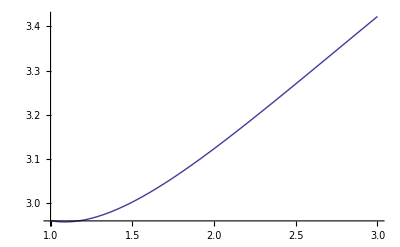

```mathematica
y0 = 1;n=4; Plot[(2 √(1+d^2))/(d/Log[(y0+d)/y0]) + (n-2)/(y0+d), {d, 1, 3}, PlotRange-> All]
```

```mathematica
(2 √(1+d^2))/(d/Log[(y0+d)/y0]) + (n-2)/(y0+d)/. {n-> 4, y0-> 1, d-> 1.}
```

2.96052

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]=Min[Flatten[Table[ F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,30}, {h,1,10}]]]
```

```mathematica
F[10,1]
```

4.66819

```mathematica
F[3,1]
```

2.46052

```mathematica
y0=1; n=10; Table[ F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,30}, {h,1,10}]
```

{{4.8939,5.53323,6.19714,6.71584,7.06874,8.4325,9.80258,11.1767,12.5534,13.9321},{4.66819,4.8939,5.24766,5.57981,5.91621,6.94823,7.99802,9.05939,10.1287,11.2037},{4.70241,4.73017,4.91896,5.12098,5.38894,6.1997,7.03847,7.89634,8.7677,9.64889},{4.80438,4.74751,4.83896,4.95218,5.15272,5.80291,6.48785,7.19763,7.92556,8.66709},{4.91514,4.8345,4.86845,4.92248,5.06786,5.59764,6.16532,6.76137,7.37892,8.01299},{5.04003,4.94687,4.94836,4.9631,5.06601,5.50387,5.98014,6.48637,7.01608,7.56434},{5.16825,5.07023,5.05147,5.04,5.11087,5.47757,5.88155,6.31565,6.77408,7.25223},{5.29501,5.19605,5.16446,5.13537,5.18214,5.49306,5.8392,6.21469,6.61452,7.03455},{5.41812,5.3203,5.28052,5.23952,5.26813,5.53473,5.83411,6.16151,6.51269,6.88403},{5.53668,5.44107,5.39608,5.34704,5.36186,5.5928,5.85401,6.14161,6.45208,6.78227},{5.65036,5.55753,5.50929,5.45486,5.45913,5.66105,5.89077,6.14516,6.4213,6.71651},{5.75879,5.66936,5.6192,5.56123,5.55739,5.7354,5.9389,6.16537,6.41237,6.67763},{5.86264,5.77656,5.72538,5.66517,5.65505,5.81316,5.99465,6.19746,6.41956,6.65904},{5.9621,5.87927,5.82768,5.76616,5.75115,5.89254,6.05538,6.238,6.43871,6.65587},{6.05741,5.97767,5.92612,5.86395,5.84513,5.97234,6.11927,6.28453,6.46673,6.66447},{6.14882,6.07203,6.02079,5.95847,5.93666,6.05175,6.18499,6.33526,6.50136,6.68212},{6.23659,6.16256,6.11186,6.04972,6.02559,6.13023,6.25163,6.38884,6.54087,6.70671},{6.32093,6.24952,6.1995,6.13779,6.11185,6.20742,6.31851,6.4443,6.58397,6.73663},{6.40209,6.33314,6.28389,6.2228,6.19545,6.28311,6.38515,6.50091,6.62965,6.77064},{6.48027,6.41363,6.36521,6.30487,6.27644,6.35715,6.45123,6.5581,6.67716,6.80776},{6.55565,6.4912,6.44364,6.38414,6.3549,6.42947,6.51649,6.61548,6.72591,6.84722},{6.62842,6.56602,6.51936,6.46075,6.43091,6.50002,6.58077,6.67273,6.77544,6.88842},{6.69874,6.63827,6.59251,6.53485,6.50457,6.56882,6.64396,6.72962,6.8254,6.93089},{6.76676,6.70812,6.66325,6.60655,6.57598,6.63588,6.70599,6.78599,6.87552,6.97423},{6.83262,6.7757,6.73172,6.676,6.64524,6.70123,6.76681,6.84169,6.92558,7.01815},{6.89644,6.84116,6.79805,6.7433,6.71245,6.76492,6.82639,6.89665,6.97542,7.06241},{6.95835,6.9046,6.86235,6.80858,6.77772,6.82698,6.88474,6.95079,7.0249,7.10682},{7.01844,6.96616,6.92475,6.87193,6.84112,6.88748,6.94186,7.00408,7.07394,7.15121},{7.07683,7.02593,6.98534,6.93346,6.90276,6.94646,6.99776,7.05648,7.12245,7.19546},{7.1336,7.08402,7.04421,6.99327,6.96271,7.00399,7.05246,7.10798,7.17038,7.23948}}

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[n_, y0_] := Min[Table[ F[n-2, y0+d] + (2. √(9+d^2))/(d/Log[(y0+d)/y0]), {d, 1,20}]]
```

```mathematica
(h-m)/(y0+d) +(√(d^2+ m^2))/(d/Log[(y0+d)/y0])
```

```mathematica
Solve[D[(h-m)/(d+y0)+(√(d^2+m^2) Log[(d+y0)/y0])/d,m]==0, m]//Simplify
```

{{m→-d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))},{m→d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))}}

```mathematica
T[d_, h_, y0_] :=Module[{ temp = -d^2+(d+y0)^2 Log[(d+y0)/y0]^2, m},
If[temp<0, Min[h/(d+y0)+(√(d^2) Log[(d+y0)/y0])/d, (h-h)/(d+y0)+(√(d^2+h^2) Log[(d+y0)/y0])/d], m=Floor[d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))]; If[m<h,Min[(h-m)/(d+y0)+(√(d^2+m^2) Log[(d+y0)/y0])/d, (h-(m+1))/(d+y0)+(√(d^2+(m+1)^2) Log[(d+y0)/y0])/d], (h-h)/(d+y0)+(√(d^2+h^2) Log[(d+y0)/y0])/d]]]
```

```mathematica
T[3,3,1.]
```

1.91612

```mathematica
ClearAll["Global`*"];

M[d_,  y0_] :=M[d, y0] = Module[{ temp = -d^2+(d+y0)^2 Log[(d+y0)/y0]^2, m},
If[temp<0, 1, Floor[d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))]]];

F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]=Min[Table[Min[F[n-2 M[d,y0], y0+d] + (2. √(M[d,y0]^2+d^2))/(d/Log[(y0+d)/y0]), F[n-2 (M[d,y0]+1), y0+d] + (2. √((M[d,y0]+1)^2+d^2))/(d/Log[(y0+d)/y0])],{d, 1,20}]];
```

```mathematica
F[100,1]
```

9.37102

```mathematica
ClearAll["Global`*"];
$RecursionLimit = 10000;
f[y0_, 0, 0] =0;
f[y0_, 0, d_] := f[y0, 0, d] = d/Log[ (y0+d)/y0];
f[y0_, h_, 0] := f[y0, h, 0] = h/y0; 
f[y0_, h_, d_] := f[y0, h, d] = Min[
Flatten[{Table[ f[y0, m, n] + f[y0+n, h-m, n-d], {m,0,h-1},{n,1,d}],
(√(h^2+d^2))/(d/Log[(y0+d)/y0])}
]
];
```

```mathematica
f[1.,1,1]
```

0.980258

```mathematica
f[1.,1,1] 2 + f[2, 2,0]
```

2.96052

```mathematica
(2 √(1+d^2))/(d/Log[(y0+d)/y0]) + (n-2)/(y0+d)
```

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]=Min[Flatten[{n,Table[ F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,50}, {h,1,n/2 }]}]];
```

```mathematica
F[10,1]
```

4.66819

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]= Module[{d, temp1= F[n-2 h, y0+1] + (2. √(h^2+1))/(1/Log[(y0+1)/y0]), temp2, result=n},
For[d=2, d<100,d++,
temp2 = F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]);
If[temp2 >= temp1, result = temp1;Break[],
temp1 = temp2];
];
Min[result, n]
]
```

```mathematica
F[3,1]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

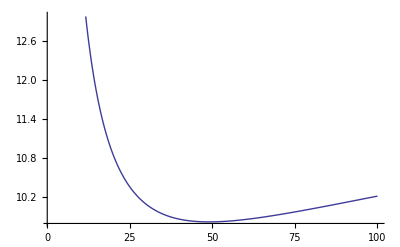

```mathematica
Plot[ (2 d)/(d/Log[(1+d)/1]) + 100/(1+d), {d, 1, 100}]
```

```mathematica
Solve[D[(h-m)/(d+y0)+(√(d^2+m^2) Log[(d+y0)/y0])/d,m]==0, m]//Simplify
```

{{m→-d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))},{m→d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))}}

```mathematica
d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))
```

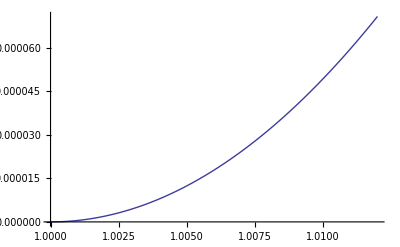

```mathematica
Plot[ Log[z] -1 + 1/z, {z, 1, 1.012}]
```

```mathematica
y0=1; h =5;
NSolve[ d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))== h, d]
```

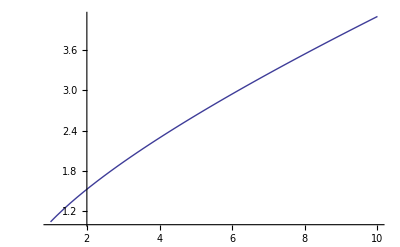

```mathematica
y0=1; h =5;
Plot[d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2)), {d, 1, 10}]
```

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 10000;
F[n_, y0_] := F[n,y0]= Module[ {d, m, result=n, mplus1, T1, T2, thisway},
For[d=1,d< 100, d++,
m = Floor[d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))];
mplus1 = m+1;

If[m>n/2, Break[]];
T1 = (2. √(d^2+m^2) Log[(d+y0)/y0])/d + F[n-2m, y0+d];
T2 = (2 √(d^2+mplus1^2) Log[(d+y0)/y0])/d +F[n-2m-2, y0+d];
m3 = Ceiling[(n-1)/2];
T3 = (2 √(d^2+m3^2) Log[(d+y0)/y0])/d +F[n-2m3, y0+d];
thisway = Min[T1, T2, T3];

If[thisway < result, result = thisway];
(* If[thisway > result, Break[]]; *)
];
result
]
```

```mathematica
F[100,1]
```

9.34387

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 10000;
F[n_, y0_] := F[n,y0]= Module[ {d, m, result=n, T},
For[d=1,d< 100, d++,
For[m=1, m<=n/2, m++,
T= (2. √(d^2+m^2) Log[(d+y0)/y0])/d + F[n-2m, y0+d];
If[T<result, result=T];
]];
result]
```

```mathematica
F[100,1]
```

4.66819

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]=Min[Flatten[Table[ F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,38}, {h,1,8}]]]
```

```mathematica
F[100,1]
```

9.22141

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 10000;
F[n_, y0_] := F[n,y0]= Module[ {d, m, result=n, T, mmax},
For[d=1,d< 100, d++,
mmax = Floor[d^2/(√(-d^2+(d+y0)^2 Log[(d+y0)/y0]^2))];
T=Min[ Table[ (2. √(d^2+m^2) Log[(d+y0)/y0])/d + F[n-2m, y0+d], {m, 1, mmax}]];
If[T<result, result=T];
]];
result]
```

```mathematica
ClearAll["Global`*"];
F[2,y0_]:= 2/y0;
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]=Min[Flatten[Table[ F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,5}, {h,1,8}]]];
G[2,y0_]:= 2/y0;
G[1,y0_]:= 1/y0;
G[0,y0_] := 0;
G[m_,y0_]/; m<0 = 0;
G[n_, y0_] := G[n,y0]=Min[Flatten[Table[ G[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,8}, {h,1,8}]]];
```

```mathematica
n=100; y0=1; F[n, y0] 
Table[ F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,5}, {h,1,8}]
 G[n, y0] 
Table[ G[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]), {d, 1,8}, {h,1,8}]
```

9.25227

{{9.76655,10.8642,12.1056,13.3944,14.7029,16.0213,17.3454,18.6719},{9.44354,10.0532,10.8648,11.7736,12.7323,13.719,14.7229,15.7368},{9.33085,9.69936,10.2462,10.903,11.6271,12.3925,13.1854,13.9966},{9.27934,9.51927,9.90223,10.3876,10.9444,11.55,12.1893,12.8525},{9.25227,9.41641,9.69417,10.0617,10.4969,10.982,11.5041,12.0535}}

9.22367

{{9.7521,10.8505,12.0927,13.3815,14.6907,16.0098,17.3343,18.6616},{9.43662,10.0464,10.8584,11.7672,12.7266,13.714,14.7182,15.7329},{9.32782,9.69654,10.2436,10.9005,11.6248,12.3909,13.1841,13.9953},{9.27812,9.51804,9.90109,10.3871,10.9441,11.5497,12.189,12.8521},{9.25217,9.41641,9.69417,10.0617,10.4969,10.982,11.5041,12.0535},{9.23711,9.35323,9.56038,9.84399,10.1894,10.5829,11.0138,11.474},{9.22829,9.31177,9.47003,9.69315,9.97081,10.2931,10.6518,11.04},{9.22367,9.284,9.40641,9.58436,9.81016,10.0773,10.3781,10.7077}}

```mathematica
F[n-2 h, y0+d] + (2 √(h^2+d^2))/(d/Log[(y0+d)/y0])/. {h-> 1, d-> 1}
```

F[-2+n,1+y0]+2 √2 Log[(1+y0)/y0]

```mathematica
ClearAll["Global`*"];
F[1,y0_]:= 1/y0;
F[0,y0_] := 0;
F[m_,y0_]/; m<0 = 0;
F[n_, y0_] := F[n,y0]=Module[{d,h, dtarget, temp, result= n/y0, previousresult, newresult, thisresult, resultA},
d=1;h=1;
previousresult =  F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]);
 result =Min[result, previousresult];
For[h=2, True, h++,
temp = F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]);
If[temp >= result,Break[], result=temp];
];
For[d=2, True, d++,
h=1; 
thisresult =  F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]);
newresult = thisresult;
For[h=2, True, h++,
temp = F[n-2 h, y0+d] + (2. √(h^2+d^2))/(d/Log[(y0+d)/y0]);
If[temp >= newresult,Break[], newresult=temp];
];
If[newresult < result, result = newresult];
If[thisresult ≥ previousresult, Break[], previousresult = thisresult];
];
resultA = result;



d=1;h=1;
previousresult =  F[n-2 h-1, y0+d] + (√(h^2+d^2))/(d/Log[(y0+d)/y0])+(√((h+1.)^2+d^2))/(d/Log[(y0+d)/y0]);
 result =Min[resultA, previousresult];
For[h=2, True, h++,
temp =  F[n-2 h-1, y0+d] + (√(h^2+d^2))/(d/Log[(y0+d)/y0])+(√((h+1.)^2+d^2))/(d/Log[(y0+d)/y0]);
If[temp >= result,Break[], result=temp];
];
For[d=2, True, d++,
h=1; 
thisresult =   F[n-2 h-1, y0+d] + (√(h^2+d^2))/(d/Log[(y0+d)/y0])+(√((h+1.)^2+d^2))/(d/Log[(y0+d)/y0]);;
newresult = thisresult;
For[h=2, True, h++,
temp = F[n-2 h-1, y0+d] + (√(h^2+d^2))/(d/Log[(y0+d)/y0])+(√((h+1.)^2+d^2))/(d/Log[(y0+d)/y0]);;
If[temp >= newresult,Break[], newresult=temp];
];
If[newresult < result, result = newresult];
If[thisresult ≥ previousresult, Break[], previousresult = thisresult];
];

result
]
```

```mathematica
F[100,1]
```

9.22371

```mathematica
Table[ Mod[i^2,5], {i, 1,4}]
```

{1,4,4,1}

```mathematica
Mod[5^20, 4]
```

1

```mathematica
5^9
```

1953125

```mathematica
1000000/7.
```

142857.

```mathematica
142857*7
```

999999

```mathematica
3*142857
```

428571

```mathematica
428570/999999-3/7
```

-1/999999

```mathematica
3*Floor[1000000/7]-1
```

428570

```mathematica
EulerPhi[91*9]
```

432

```mathematica
Divisors[432]
```

{1,2,3,4,6,8,9,12,16,18,24,27,36,48,54,72,108,144,216,432}

```mathematica
Mod[10^6, 91*9]
```

1

```mathematica
FactorInteger[703]
```

{{19,1},{37,1}}

```mathematica
Mod[10^6, 91]
```

1

```mathematica
91-1
```

90

```mathematica
EulerPhi[91]
```

72

```mathematica
f[n_, k_] :=  Exp[k/n]-1.
```

```mathematica
f[200,6] + f[200,75] + f[200,89] + f[200,226]+0.
```

3.14159

```mathematica
π - (f[200,6] + f[200,75] + f[200,89] )
```

2.09566

```mathematica
NSolve[  f[200,x] ==2.0956565091854085,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→226.}}

```mathematica
f[200,1.]
```

0.00501252

```mathematica
FactorInteger[10000]
```

{{2,4},{5,4}}

```mathematica
2^4
```

```mathematica
16*625
```

10000

```mathematica
5^4
```

625

```mathematica
ClearAll["Global`*"];
f[n_, k_] :=  f[n,k] =Exp[k/n]-1.;
limit =16;
error = 1;
For[i=1,i<limit,i++,
For[j=i,j<limit,j++,
For[k=j,k<limit,k++,
diff = π - f[limit,i] - f[limit,j] - f[limit,k];
If[diff<0, Break[]];
m = Floor[Log[1+diff]*limit];
error1 = Abs[diff - f[limit, m]];
If[error1 < error, error=error1; Print[{i,j,k,m,error}]];
m = m+1;
error2 = Abs[diff - f[limit, m]];
If[error2 < error, error=error2; Print[{i,j,k,m,error}]];
]]]
```

{1,1,1,21,0.232659}

{1,1,1,22,0.00696745}

{1,1,12,17,0.00200777}

{1,2,6,20,0.00138463}

{3,3,8,18,0.000194035}

{4,7,9,15,0.0000928232}

```mathematica
NSolve[Exp[k/200.]-1 == π - 3 Exp[1/200]+3, k]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{k→283.489}}

```mathematica
ClearAll["Global`*"];
f[n_, k_] :=  f[n,k] =Exp[k/n]-1.;
limit =10000;
error = 1;
For[i=199,i<300,i++,
Print[i];
For[j=i,j<400,j++,
For[k=j,k<10000,k++,
diff = π - f[limit,i] - f[limit,j] - f[limit,k];
If[diff<0, Break[]];
m = Floor[Log[1+diff]*limit];
error1 = Abs[diff - f[limit, m]];
If[error1 < error, error=error1; Print[{i,j,k,m,error}]];
m = m+1;
error2 = Abs[diff - f[limit, m]];
If[error2 < error, error=error2; Print[{i,j,k,m,error}]];
]]]
```

199

{199,199,199,14064,0.000058204}

{199,199,200,14064,0.000043811}

{199,199,251,14051,0.0000420321}

{199,199,255,14050,0.0000393561}

{199,199,259,14049,0.0000364751}

{199,199,263,14048,0.0000333892}

{199,199,267,14047,0.0000300983}

{199,199,271,14046,0.0000266024}

{199,199,275,14045,0.0000229012}

{199,199,279,14044,0.0000189949}

{199,199,283,14043,0.0000148834}

{199,199,287,14042,0.0000105665}

{199,199,291,14041,6.04423×10^-6}

{199,199,295,14040,1.31652×10^-6}

{199,199,1369,13749,7.0286×10^-7}

{199,199,2058,13540,3.92264×10^-7}

{199,199,2385,13434,5.48284×10^-8}

{199,199,7895,10644,2.53465×10^-9}

{199,208,4187,12755,1.63032×10^-9}

{199,213,5086,12346,1.55614×10^-9}

{199,272,1801,13601,2.72016×10^-10}

{199,395,665,13894,1.4517×10^-10}

200

{200,242,8328,10286,1.1553×10^-10}

{200,303,2211,13463,4.59277×10^-11}

201

{201,326,1151,13778,2.19713×10^-11}

{201,366,7379,10961,1.14022×10^-11}

202

203

204

205

206

207

208

209

{209,333,4542,12561,9.53371×10^-12}

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

{225,336,508,13944,4.22506×10^-12}

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

```mathematica
Table[ Exp[k/200] - 1. - π/4, {k, 100, 120}]
```

{-0.136677,-0.128413,-0.120107,-0.11176,-0.103371,-0.0949393,-0.0864659,-0.0779499,-0.0693913,-0.0607898,-0.0521451,-0.0434572,-0.0347257,-0.0259504,-0.0171311,-0.00826764,0.000640267,0.00959282,0.0185903,0.0276328,0.0367206}

```mathematica
Table[ Abs[Exp[k/10000] - Exp[(k+1.)/10000]], {k, 0,1}]
```

{0.000100005,0.000100015}

```mathematica
Exp[1.]-1
```

1.71828

```mathematica
ClearAll["Global`*"];
f[n_, k_] :=  f[n,k] =Exp[k/n]-1.-π/4;
limit =200;
error = 1000000;
For[i=1,i<limit,i++,
j = Floor[limit * Log[2+π/2 - Exp[i/limit]]];
If[j<-1, Continue[]];
sum =Abs[ f[limit,j] + f[limit, i]];
If[error>sum, error=sum; Print[{i,j,error}]];
j=j+1;
sum = Abs[f[limit,j] + f[limit, i]];
If[error>sum, error=sum; Print[{i,j,error}]];
]
```

{1,188,0.00580239}

{2,188,0.000764741}

{7,186,0.00066744}

{12,184,0.00033061}

{49,166,0.000143727}

```mathematica
ClearAll["Global`*"];
f[n_, k_] :=  f[n,k] =Exp[k/n]-1.+π/4;
limit =200;
error = 1000;
For[i=1,i<limit,i++,
Print[i];
For[j=i,j<limit,j++,
For[k=j,k<limit,k++,
sum = f[limit, i] + f[limit, j] +  f[limit,k];
m = Floor[Log[1+sum-π/4]*limit];
error1 =Abs[ sum+ f[limit, m]];
If[ error1 < error, error=error1; Print[{i,j,k,m,error}]];
m = m+1;
error2 = Abs[sum + f[limit, m]];
If[error2 < error, error=error2; Print[{i,j,k,m,error}]];
]]]
```

1

{1,1,1,190,4.74234}

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

```mathematica
ClearAll["Global`*"];
n=200;
f[k_] :=  f[k] =Exp[k/n]-1.+π/4;
Table[ f[i]+f[j], {i=
```

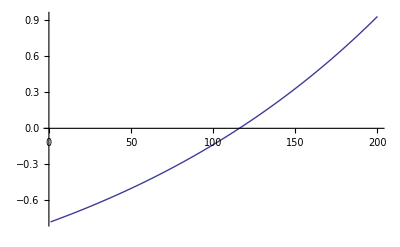

```mathematica
n=200; Plot[ Exp[k/n]-1-π/4, {k, 1, 200}]
```

```mathematica
3 (1/4.)^3
```

0.046875

```mathematica
p=3;
Table[ (n^3 + n^2 p)^(1/3), {n, 1, 1000}]
```

```mathematica
Solve[ n^3 + n^2 p == (n+m^2)^3, n]  //Simplify
```

{{n→(-3 m^4+√(-3 m^8+4 m^6 p))/(6 m^2-2 p)},{n→(3 m^4+√(-3 m^8+4 m^6 p))/(2 (-3 m^2+p))}}

```mathematica
PrimePi[1000000]
```

78498

```mathematica
?MemberQ
```

MemberQ[list,form] returns True if an element of list matches form, and False otherwise. 
MemberQ[list,form,levelspec] tests all parts of list specified by levelspec.

```mathematica
p=7
IntegerQ /@ Table[(3 m^4+√(-3 m^8+4 m^6 p))/(2 (-3 m^2+p)), {m, 1,√(p/3)}]
```

7

{True}

```mathematica
num=0;
For[i=3, i<PrimePi[1000000], ++i,
If[Mod[i,10000]==0, Print[i]];
p=Prime[i];
If[Mod[p,3]==2, Continue[]];
If[MemberQ[IntegerQ /@Table[(3 m^4+√(-3 m^8+4 m^6 p))/(2 (-3 m^2+p)), {m, 1,√(p/3.)}], True], num++];
];
num
```

10000

20000

```mathematica
1^3+ 1^2*7
```

8

```mathematica
-3 m^2+4  p/. p-> 3k+1
```

4 (1+3 k)-3 m^2

```mathematica
F[p_] := Module[{k, result=-1}, 
For[k=1, k<10000, k++,
If[IntegerQ[√(-3 k^2+4 k p)], result=k; Break[]];];
result
]
```

```mathematica
F[7]
```

1

```mathematica
Table[{Prime[n],F[Prime[n]]}, {n, 3, 100}]
```

{{5,5},{7,1},{11,11},{13,1},{17,17},{19,4},{23,23},{29,29},{31,1},{37,9},{41,41},{43,1},{47,47},{53,53},{59,59},{61,16},{67,4},{71,71},{73,1},{79,9},{83,83},{89,89},{97,9},{101,101},{103,4},{107,107},{109,25},{113,113},{127,36},{131,131},{137,137},{139,9},{149,149},{151,25},{157,1},{163,9},{167,167},{173,173},{179,179},{181,16},{191,191},{193,49},{197,197},{199,4},{211,1},{223,36},{227,227},{229,25},{233,233},{239,239},{241,1},{251,251},{257,257},{263,263},{269,269},{271,81},{277,49},{281,281},{283,36},{293,293},{307,1},{311,311},{313,9},{317,317},{331,100},{337,64},{347,347},{349,9},{353,353},{359,359},{367,81},{373,16},{379,49},{383,383},{389,389},{397,121},{401,401},{409,64},{419,419},{421,1},{431,431},{433,121},{439,25},{443,443},{449,449},{457,49},{461,461},{463,1},{467,467},{479,479},{487,4},{491,491},{499,49},{503,503},{509,509},{521,521},{523,81},{541,16}}

```mathematica
ClearAll["Global`*"];
Timing[
num=0;
imax = PrimePi[1000000];
For[i=3, i<imax, ++i,
p=Prime[i];
If[Mod[p,3]==2, Continue[]];

For[m=Floor[√(p/3.)], m≥1, --m,
t = √(-3 m^2+4 p);
If[!IntegerQ[t], Continue[]];
If[IntegerQ[(3 m^4+t m^3)/(2 (-3 m^2+p))], ++num; Break[]];
];
];
num
]
```

{237.30872,173}

```mathematica
Table[GCD[n, n+37], {n, 1,100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,37,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,37,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
DayMatchQ[DateList[],"Saturday"]
```

DayMatchQ[{2014,3,2,18,5,35.4785429},Saturday]

```mathematica
days = DayRange[{1901,1,1},{2000,12,31}];
Length[Select[days, (#[[3]]==1&& DayName[#]==Sunday)&]]
```

171

```mathematica
1/2n(n-1)+1/. n-> 9
```

37

```mathematica
ClearAll["Global`*"];
TripletQ[r_, c_] := Module[{},
If[c==1,


n=8;
begin = 1/2 (n-1) n +1
end = 1/2 n(n+1)
imin = PrimePi[begin-1]+1
imax = PrimePi[end-1]
sum = 0;
For[i=imin, i≤ imax, ++i,
p = Prime[i];
If[TripletQ[n,p-begin+1], sum = sum+p];
];
sum
```

29

36

10

11

0

```mathematica
ClearAll["Global`*"];
G[{}]=0;
G[{1}]=1;
G[{1,0}]=2;
G[list_] := Module[{list1, list2, list3, result},
If[Length[list]==1, Return[1]];
If[list[[1]]>=3, Return[0]]; 
If[list[[1]]==2, list1=Drop[list,1];Return[ 1+G[list1]]];
If[ list[[1]] ==0, list1 = Drop[list,1]; Return[G[list1]];];
list1 = Drop[list,1];
While[list[[1]]==0;
list1 = Drop[list1,1];
];
list2 =list;
list2[[1]]==0;
list2[[2]]=list[[2]]+2;
list2 = Drop[list2, 1];
Print[{list1,list2}];
G[list1] + G[list2]
]
G[{1,1}]
```

{{},{3}}

1

```mathematica
ClearAll["Global`*"];
f[0]=0;
f[1]=1;
f[3]=3;
f[n_] := f[n]=If[EvenQ[n], f[n/2],If[Mod[n,4]==1, 2 f[(n+1)/2]-f[(n-1)/4], 3f[(n-1)/2]-2f[(n-3)/4]]]
 Table[Sum[ f[i], {i,0,3n}], {n, 0, 100}]
```

{0,5,14,31,52,85,112,163,208,265,310,375,450,573,636,747,840,945,1026,1131,1224,1365,1464,1659,1830,2049,2220,2415,2574,2829,2964,3195,3384,3585,3738,3939,4116,4389,4506,4719,4908,5145,5334,5591,5882,6365,6608,7043,7406,7817,8132,8543,8906,9461,9668,10067,10418,10865,11216,11615,11942,12461,12740,13211,13592,13985,14282,14675,15020,15557,15782,16199,16568,17033,17402,17795,18104,18605,18866,19319,19700,20129,20462,20891,21272,21845,22232,23003,23678,24545,25220,25991,26618,27629,28160,29075,29822,30617,31220,32015,32714}

```mathematica
Differences[Out[6]]
```

```mathematica
Table[FromDigits[Reverse[IntegerDigits[i,2]],2],{i,0,80}]
```

{0,1,1,3,1,5,3,7,1,9,5,13,3,11,7,15,1,17,9,25,5,21,13,29,3,19,11,27,7,23,15,31,1,33,17,49,9,41,25,57,5,37,21,53,13,45,29,61,3,35,19,51,11,43,27,59,7,39,23,55,15,47,31,63,1,65,33,97,17,81,49,113,9,73,41,105,25,89,57,121,5}

```mathematica
Table[f[i],{i,1,100}]
```

{1,1,3,1,5,3,7,1,9,5,13,3,11,7,15,1,17,9,25,5,21,13,29,3,19,11,27,7,23,15,31,1,33,17,49,9,41,25,57,5,37,21,53,13,45,29,61,3,35,19,51,11,43,27,59,7,39,23,55,15,47,31,63,1,65,33,97,17,81,49,113,9,73,41,105,25,89,57,121,5,69,37,101,21,85,53,117,13,77,45,109,29,93,61,125,3,67,35,99,19}

```mathematica
list = Table[ Sum[ f[4i+3],{i,0,n}], {n, 1, 100}]
```

{10,23,38,63,92,119,150,199,256,309,370,421,480,535,598,695,808,913,1034,1135,1252,1361,1486,1585,1700,1807,1930,2033,2152,2263,2390,2583,2808,3017,3258,3459,3692,3909,4158,4355,4584,4797,5042,5247,5484,5705,5958,6153,6380,6591,6834,7037,7272,7491,7742,7941,8172,8387,8634,8841,9080,9303,9558,9943,10392,10809,11290,11691,12156,12589,13086,13479,13936,14361,14850,15259,15732,16173,16678,17067,17520,17941,18426,18831,19300,19737,20238,20635,21096,21525,22018,22431,22908,23353,23862,24249,24700,25119,25602,26005}

```mathematica
Differences[list]
```

{28,36,52,68,60,76,100,132,116,148,108,140,124,156,196,260,228,292,212,276,244,308,204,268,236,300,220,284,252,316,388,516,452,580,420,548,484,612,404,532,468,596,436,564,500,628,396,524,460,588,428,556,492,620,412,540,476,604,444,572,508,636,772,1028,900,1156,836,1092,964,1220,804,1060,932,1188,868,1124,996,1252,788,1044,916,1172,852,1108,980,1236,820,1076,948,1204,884,1140,1012,1268,780,1036,908,1164,844}

```mathematica
Mod[3^37,16]
```

3

```mathematica
Log[2., 3^37]
```

58.6436

```mathematica
?Differences
```

Differences[list] gives the successive differences of elements in list. 
Differences[list,n] gives the n^th differences of list. 
Differences[list,n,s] gives the differences of elements step s apart.
Differences[list,{n_1,n_2,…}] gives the successive n_k^th differences at level k in a nested list.

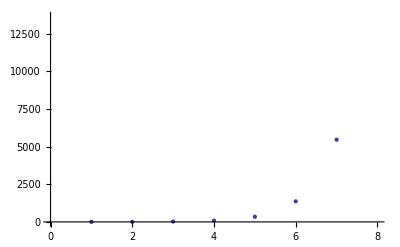

```mathematica
ListPlot[Table[ Sum[ f[i],{i,0,2^n}], {n, 1, 8}]]
```

```mathematica
3^37
```

450283905890997363

```mathematica
Table[ Sum[ f[i],{i,0,2^n}], {n, 1, 12}]
```

{2,6,22,86,342,1366,5462,21846,87382,349526,1398102,5592406}

```mathematica
ClearAll["Global`*"];
f[0]=0;
f[1]=1;
f[3]=3;
f[n_] := f[n]=If[EvenQ[n], f[n/2],If[Mod[n,4]==1, 2 f[(n+1)/2]-f[(n-1)/4], 3f[(n-1)/2]-2f[(n-3)/4]]]
list = Table[ Sum[ f[i],{i,0,2^n}], {n, 1, 10}]
Table[(4^n+2)/3, {n, 1, 10}]
```

{2,6,22,86,342,1366,5462,21846,87382,349526}

{2,6,22,86,342,1366,5462,21846,87382,349526}

```mathematica
f[2^58+2]
```

144115188075855873

```mathematica
f[2^58+4]
```

72057594037927937

```mathematica
IntegerDigits[3^37,2]
```

{1,1,0,0,0,1,1,1,1,1,1,1,0,1,1,1,0,1,0,1,1,0,1,0,0,1,1,1,0,1,0,0,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,0,1,1,1,0,0,1,1}

```mathematica
ClearAll["Global`*"];
f[0]=0;
f[1]=1;
f[3]=3;
f[n_] := f[n]=If[EvenQ[n], f[n/2],If[Mod[n,4]==1, 2 f[(n+1)/2]-f[(n-1)/4], 3f[(n-1)/2]-2f[(n-3)/4]]]
list = Table[ Sum[ f[4 i],{i,0,n}], {n, 1, 120}]
Log[list 1.]
```

{1,2,5,6,11,14,21,22,31,36,49,52,63,70,85,86,103,112,137,142,163,176,205,208,227,238,265,272,295,310,341,342,375,392,441,450,491,516,573,578,615,636,689,702,747,776,837,840,875,894,945,956,999,1026,1085,1092,1131,1154,1209,1224,1271,1302,1365,1366,1431,1464,1561,1578,1659,1708,1821,1830,1903,1944,2049,2074,2163,2220,2341,2346,2415,2452,2553,2574,2659,2712,2829,2842,2919,2964,3073,3102,3195,3256,3381,3384,3451,3486,3585,3604,3687,3738,3853,3864,3939,3982,4089,4116,4207,4266,4389,4396,4467,4506,4609,4632,4719,4774,4893,4908}

{0.,0.693147,1.60944,1.79176,2.3979,2.63906,3.04452,3.09104,3.43399,3.58352,3.89182,3.95124,4.14313,4.2485,4.44265,4.45435,4.63473,4.7185,4.91998,4.95583,5.09375,5.17048,5.32301,5.33754,5.42495,5.47227,5.57973,5.6058,5.68698,5.73657,5.83188,5.83481,5.92693,5.97126,6.08904,6.10925,6.19644,6.24611,6.35089,6.35957,6.42162,6.4552,6.53524,6.55393,6.61607,6.65415,6.72982,6.7334,6.77422,6.79571,6.85118,6.86276,6.90675,6.93342,6.98934,6.99577,7.03086,7.05099,7.09755,7.10988,7.14756,7.17166,7.21891,7.21964,7.26613,7.28893,7.35308,7.36391,7.41397,7.44308,7.50714,7.51207,7.55119,7.5725,7.62511,7.63723,7.67925,7.70526,7.75833,7.76047,7.78945,7.80466,7.84502,7.85322,7.88571,7.90544,7.94768,7.95226,7.979,7.99429,8.03041,8.0398,8.06934,8.08825,8.12593,8.12681,8.14642,8.15651,8.18451,8.1898,8.21257,8.22631,8.25661,8.25946,8.27868,8.28954,8.31606,8.32264,8.34451,8.35843,8.38686,8.38845,8.40447,8.41317,8.43577,8.44074,8.45935,8.47094,8.49556,8.49862}

```mathematica
Table[ Sum[ f[i], {i, 2^n+1, 2^n+1+32}], {n,1,6}]
```

{439,485,593,789,1089,2085}

```mathematica
439*5
```

2195

```mathematica
265/5
```

53

```mathematica
20128./265
```

75.9547

```mathematica
1680033./20129
```

83.4633

```mathematica
143488409/1680033.
```

85.4081

```mathematica
f[2^6+1]
f[1]
```

65

1

```mathematica
Table[f[2^n+4Log], {n,1,10}]
```

{3,1,3,5,9,17,33,65,129,257}

```mathematica
Log[2,64]
```

6

```mathematica
ClearAll["Global`*"];
f[0]=0;
f[1]=1;
f[3]=3;
f[n_] := f[n]=If[EvenQ[n], f[n/2],If[Mod[n,4]==1, 2 f[(n+1)/2]-f[(n-1)/4], 3f[(n-1)/2]-2f[(n-3)/4]]]
list = Table[ Sum[ f[i],{i,0,3^n}], {n, 1, 12, 2}]
Log[list 1.]
```

52.649457195309171449788242873237256548120945433014

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.